```mathematica
ClearAll["Global`*"]
Subscript[Q, 2]=Subscript[c, 3]/(Subscript[x, 3]-Subscript[A, 3])
Subscript[Q, 1]=  Subscript[c, 2]/(Subscript[x, 2]-Subscript[A, 2]) + Subscript[Q, 2](Subscript[x, 2]+Subscript[B, 2])/(Subscript[x, 2]-Subscript[A, 2])
P=Subscript[c, 1]/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[Q, 1](Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1])
xxi={Subscript[x, 1]->Subscript[A, 1]+Subscript[ξ, 1],Subscript[x, 2]->Subscript[A, 2]+Subscript[ξ, 2],Subscript[x, 3]->Subscript[A, 3]+Subscript[ξ, 3]}
xix={Subscript[ξ, 1]->Subscript[x, 1]-Subscript[A, 1],Subscript[ξ, 2]->Subscript[x, 2]-Subscript[A, 2],Subscript[ξ, 3]->Subscript[x, 3]-Subscript[A, 3]}
alphasubs = {Subscript[A, 1]->Subscript[α, 1]- Subscript[B, 1],Subscript[A, 2]->Subscript[α, 2]- Subscript[B, 2]}
asubs={Subscript[α, 1]->Subscript[A, 1]+Subscript[B, 1],Subscript[α, 2]->Subscript[A, 2]+Subscript[B, 2]}
```

c_3/(-A_3+x_3)

c_2/(-A_2+x_2)+(c_3 (B_2+x_2))/((-A_2+x_2) (-A_3+x_3))

c_1/(-A_1+x_1)+((B_1+x_1) (c_2/(-A_2+x_2)+(c_3 (B_2+x_2))/((-A_2+x_2) (-A_3+x_3))))/(-A_1+x_1)

{x_1→A_1+ξ_1,x_2→A_2+ξ_2,x_3→A_3+ξ_3}

{ξ_1→-A_1+x_1,ξ_2→-A_2+x_2,ξ_3→-A_3+x_3}

{A_1→-B_1+α_1,A_2→-B_2+α_2}

{α_1→A_1+B_1,α_2→A_2+B_2}

```mathematica
Pt=P/.{Subscript[x, 1]->t Subscript[x, 1],Subscript[x, 2]->t Subscript[x, 2],Subscript[x, 3]->t Subscript[x, 3]};
Ps = P/.{Subscript[x, 1]->Subscript[x, 1]+s};
Pt=Pt/.{t->1+s/(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3])};
Ps=Ps/.xxi;
Pt=Pt/.xxi;
sfun=Numerator[Factor[(Pt-Ps)]/s];
bs[0]=Factor[Coefficient[sfun,s,0]];
bs[1]=Factor[Coefficient[sfun,s,1]];
bs[2]=Factor[Coefficient[sfun,s,2]];
bs[3]=Factor[Coefficient[sfun,s,3]];
```

```mathematica
(*3 1 2*)
sol1=Solve[D[P,Subscript[x, 2]]==D[P,Subscript[x, 3]],Subscript[c, 3]]/.xxi/.alphasubs//Factor (* 2 of 3*)
sol2=Solve[D[P,Subscript[x, 1]]==D[P,Subscript[x, 3]],Subscript[c, 1]]/.xxi/.alphasubs//Factor  (*1 2 of 3*)
sol3=Solve[D[P,Subscript[x, 1]]==D[P,Subscript[x, 2]],Subscript[c, 2]]/.xxi/.alphasubs//Factor (*1 2 of 3*)
Factor[sol1/.sol2]//FullSimplify
Factor[sol1/.sol3]//FullSimplify
Factor[sol2/.sol3]//FullSimplify
Factor[sol2/.sol1]//FullSimplify
Factor[sol3/.sol1]//FullSimplify
Factor[sol3/.sol2]//FullSimplify
sol1
sol2
sol3
Subscript[c, 3]==(Subscript[c, 3]/.sol1[[1]][[1]])
c2sol=Solve[Subscript[c, 3]==(Subscript[c, 3]/.sol1[[1]][[1]]),Subscript[c, 2]]
Factor[sol2/.c2sol]
c3c1sol=Solve[Subscript[c, 1]==(Subscript[c, 1]/.Factor[sol2[[1]][[1]]/.c2sol]),Subscript[c, 3]]
c2c1sol=c2sol/.c3c1sol
```

{{c_3→(c_2 ξ_3^2)/(α_2 ξ_2+ξ_2^2-α_2 ξ_3)}}

{{c_1→(c_3 α_1 α_2 ξ_1+c_3 α_2 ξ_1^2+c_3 α_1 ξ_1 ξ_2+c_3 ξ_1^2 ξ_2-c_3 α_1 α_2 ξ_3-c_3 α_1 ξ_2 ξ_3-c_2 α_1 ξ_3^2)/(ξ_2 ξ_3^2)}}

{{c_2→-(c_3 α_1 α_2 ξ_1+c_3 α_2 ξ_1^2-c_3 α_1 α_2 ξ_2-c_3 α_1 ξ_2^2-c_1 ξ_2^2 ξ_3)/((α_1 ξ_1+ξ_1^2-α_1 ξ_2) ξ_3)}}

{{{c_3→(c_2 ξ_3^2)/(ξ_2^2+α_2 (ξ_2-ξ_3))}}}

{{{c_3→(ξ_3 (c_3 (-α_2 ξ_1 (α_1+ξ_1)+α_1 α_2 ξ_2+α_1 ξ_2^2)+c_1 ξ_2^2 ξ_3))/((ξ_1^2+α_1 (ξ_1-ξ_2)) (ξ_2^2+α_2 (ξ_2-ξ_3)))}}}

{{{c_1→(c_1 α_1 ξ_2^2 ξ_3^2+c_3 ξ_1 (α_1+ξ_1) (-(ξ_1^2+α_1 (ξ_1-ξ_2)) (α_2+ξ_2)+α_1 ξ_2 ξ_3))/(ξ_2 (-ξ_1 (α_1+ξ_1)+α_1 ξ_2) ξ_3^2)}}}

{{{c_1→(c_2 ((ξ_1^2+α_1 (ξ_1-ξ_2)) (α_2+ξ_2)-α_1 ξ_2 ξ_3))/(ξ_2^3+α_2 ξ_2 (ξ_2-ξ_3))}}}

{{{c_2→(c_1 ξ_2^2 (ξ_2^2+α_2 (ξ_2-ξ_3))+c_2 (-α_2 ξ_1 (α_1+ξ_1)+α_1 α_2 ξ_2+α_1 ξ_2^2) ξ_3)/((ξ_1^2+α_1 (ξ_1-ξ_2)) (ξ_2^2+α_2 (ξ_2-ξ_3)))}}}

{{{c_2→(c_3 ξ_1 (α_1+ξ_1) (ξ_2^2+α_2 (ξ_2-ξ_3))-c_2 α_1 ξ_2 ξ_3^2)/((ξ_1^2+α_1 (ξ_1-ξ_2)) ξ_3^2)}}}

{{c_3→(c_2 ξ_3^2)/(α_2 ξ_2+ξ_2^2-α_2 ξ_3)}}

{{c_1→(c_3 α_1 α_2 ξ_1+c_3 α_2 ξ_1^2+c_3 α_1 ξ_1 ξ_2+c_3 ξ_1^2 ξ_2-c_3 α_1 α_2 ξ_3-c_3 α_1 ξ_2 ξ_3-c_2 α_1 ξ_3^2)/(ξ_2 ξ_3^2)}}

{{c_2→-(c_3 α_1 α_2 ξ_1+c_3 α_2 ξ_1^2-c_3 α_1 α_2 ξ_2-c_3 α_1 ξ_2^2-c_1 ξ_2^2 ξ_3)/((α_1 ξ_1+ξ_1^2-α_1 ξ_2) ξ_3)}}

c_3==(c_2 ξ_3^2)/(α_2 ξ_2+ξ_2^2-α_2 ξ_3)

{{c_2→(c_3 (α_2 ξ_2+ξ_2^2-α_2 ξ_3))/ξ_3^2}}

{{{c_1→-(c_3 (-α_1 α_2 ξ_1-α_2 ξ_1^2+α_1 α_2 ξ_2-α_1 ξ_1 ξ_2-ξ_1^2 ξ_2+α_1 ξ_2^2+α_1 ξ_2 ξ_3))/(ξ_2 ξ_3^2)}}}

{{c_3→-(c_1 ξ_2 ξ_3^2)/(-α_1 α_2 ξ_1-α_2 ξ_1^2+α_1 α_2 ξ_2-α_1 ξ_1 ξ_2-ξ_1^2 ξ_2+α_1 ξ_2^2+α_1 ξ_2 ξ_3)}}

{{{c_2→-(c_1 ξ_2 (α_2 ξ_2+ξ_2^2-α_2 ξ_3))/(-α_1 α_2 ξ_1-α_2 ξ_1^2+α_1 α_2 ξ_2-α_1 ξ_1 ξ_2-ξ_1^2 ξ_2+α_1 ξ_2^2+α_1 ξ_2 ξ_3)}}}

```mathematica
c3sol=Solve[D[P,Subscript[x, 2]]==D[P,Subscript[x, 3]],Subscript[c, 3]]/.xxi//Factor
x3bnd2=Solve[Denominator[(Subscript[c, 3]/.c3sol[[1]])/Subscript[c, 2]]==0,Subscript[ξ, 3]]//Simplify
c1sol=Solve[D[P,Subscript[x, 1]]==D[P,Subscript[x, 3]],Subscript[c, 1]]/.xxi//Factor
Collect[Numerator[Subscript[c, 1]/.c1sol[[1]]],Subscript[c, 2],Factor]
c1bdyc2=Factor[Collect[Numerator[Subscript[c, 1]/.c1sol[[1]]],Subscript[c, 3]]/.c3sol[[1]]]
Numerator[c1bdyc2 / Subscript[c, 2]/Subscript[ξ, 3]/Subscript[ξ, 3]]
```

{{c_3→(c_2 ξ_3^2)/(A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3)}}

{{ξ_3→(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)}}

{{c_1→1/(ξ_2 ξ_3^2)(A_1 A_2 c_3 ξ_1+A_2 B_1 c_3 ξ_1+A_1 B_2 c_3 ξ_1+B_1 B_2 c_3 ξ_1+A_2 c_3 ξ_1^2+B_2 c_3 ξ_1^2+A_1 c_3 ξ_1 ξ_2+B_1 c_3 ξ_1 ξ_2+c_3 ξ_1^2 ξ_2-A_1 A_2 c_3 ξ_3-A_2 B_1 c_3 ξ_3-A_1 B_2 c_3 ξ_3-B_1 B_2 c_3 ξ_3-A_1 c_3 ξ_2 ξ_3-B_1 c_3 ξ_2 ξ_3-A_1 c_2 ξ_3^2-B_1 c_2 ξ_3^2)}}

-(A_1+B_1) c_2 ξ_3^2+c_3 (A_2+B_2+ξ_2) (A_1 ξ_1+B_1 ξ_1+ξ_1^2-A_1 ξ_3-B_1 ξ_3)

(c_2 ξ_3^2 (-A_1 A_2 ξ_1-A_2 B_1 ξ_1-A_1 B_2 ξ_1-B_1 B_2 ξ_1-A_2 ξ_1^2-B_2 ξ_1^2+A_1 A_2 ξ_2+A_2 B_1 ξ_2+A_1 B_2 ξ_2+B_1 B_2 ξ_2-A_1 ξ_1 ξ_2-B_1 ξ_1 ξ_2-ξ_1^2 ξ_2+A_1 ξ_2^2+B_1 ξ_2^2+A_1 ξ_2 ξ_3+B_1 ξ_2 ξ_3))/(-A_2 ξ_2-B_2 ξ_2-ξ_2^2+A_2 ξ_3+B_2 ξ_3)

-A_1 A_2 ξ_1-A_2 B_1 ξ_1-A_1 B_2 ξ_1-B_1 B_2 ξ_1-A_2 ξ_1^2-B_2 ξ_1^2+A_1 A_2 ξ_2+A_2 B_1 ξ_2+A_1 B_2 ξ_2+B_1 B_2 ξ_2-A_1 ξ_1 ξ_2-B_1 ξ_1 ξ_2-ξ_1^2 ξ_2+A_1 ξ_2^2+B_1 ξ_2^2+A_1 ξ_2 ξ_3+B_1 ξ_2 ξ_3

```mathematica
bs0opt=Factor[bs[0]/.c3sol[[1]];
bs0opt=bs0opt/.c2sol[[1]]]
list=FactorList[Numerator[bs0opt]]
list[[7]][[1]]
```

Part::partd: Part specification c2sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {c2sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of bs0opt/.c2sol⟦1⟧.

Hold[bs0opt/.c2sol⟦1⟧]

{{1,1},{Hold[bs0opt/.c2sol⟦1⟧],1}}

Part::partw: Part 7 of {{1,1},{Hold[bs0opt/.c2sol⟦1⟧],1}} does not exist.

{{1,1},{Hold[bs0opt/.c2sol⟦1⟧],1}}

```mathematica
x3bnd2[[1]]/.alphasubs
X3bnd = Subscript[ξ, 3]/.(x3bnd2[[1]]/.alphasubs)
X3bnd=(Subscript[α, 2]+Subscript[ξ, 2])(Subscript[α, 1](Subscript[ξ, 1]+Subscript[ξ, 2]) + Subscript[ξ, 1] Subscript[ξ, 1])/(2 Subscript[α, 2] + Subscript[ξ, 2])/Subscript[α, 1]
Factor[bs[0]/.{Subscript[ξ, 3]->X3bnd z/(1+z)}]
bs[0]
```

{ξ_3→(ξ_2 (α_2+ξ_2))/α_2}

(ξ_2 (α_2+ξ_2))/α_2

((α_2+ξ_2) (ξ_1^2+α_1 (ξ_1+ξ_2)))/(α_1 (2 α_2+ξ_2))

-((2 A_1 α_1 α_2+2 z A_1 α_1 α_2+18+α_1 ξ_2^2+2 z α_1 ξ_2^2)^2 (4 z A_1 A_2^2 c_3 α_1^3 α_2^3 ξ_1^2+8 z^2 A_1 A_2^2 c_3 α_1^3 α_2^3 ξ_1^2+2548))/((1+z)^5 α_1^5 (2 α_2+ξ_2)^5)
 |  |  |  |

-(A_1+A_2+A_3+ξ_1+ξ_2+ξ_3)^2 (A_1 A_2 A_3 c_3 ξ_1 ξ_2+A_2 A_3 B_1 c_3 ξ_1 ξ_2+A_1 A_3 B_2 c_3 ξ_1 ξ_2+A_3 B_1 B_2 c_3 ξ_1 ξ_2+A_2 A_3 c_3 ξ_1^2 ξ_2+A_3 B_2 c_3 ξ_1^2 ξ_2+A_1 A_3 c_3 ξ_1 ξ_2^2+A_3 B_1 c_3 ξ_1 ξ_2^2+A_3 c_3 ξ_1^2 ξ_2^2+A_1 A_2^2 c_3 ξ_1 ξ_3+A_2^2 B_1 c_3 ξ_1 ξ_3+A_1 A_2 B_2 c_3 ξ_1 ξ_3+A_2 B_1 B_2 c_3 ξ_1 ξ_3+A_2^2 c_3 ξ_1^2 ξ_3+A_2 B_2 c_3 ξ_1^2 ξ_3-A_1 A_2^2 c_3 ξ_2 ξ_3-A_1 A_2 A_3 c_3 ξ_2 ξ_3-A_2^2 B_1 c_3 ξ_2 ξ_3-A_2 A_3 B_1 c_3 ξ_2 ξ_3-A_1 A_2 B_2 c_3 ξ_2 ξ_3-A_1 A_3 B_2 c_3 ξ_2 ξ_3-A_2 B_1 B_2 c_3 ξ_2 ξ_3-A_3 B_1 B_2 c_3 ξ_2 ξ_3+2 A_1 A_2 c_3 ξ_1 ξ_2 ξ_3+2 A_2 B_1 c_3 ξ_1 ξ_2 ξ_3+2 A_1 B_2 c_3 ξ_1 ξ_2 ξ_3+2 B_1 B_2 c_3 ξ_1 ξ_2 ξ_3+2 A_2 c_3 ξ_1^2 ξ_2 ξ_3+2 B_2 c_3 ξ_1^2 ξ_2 ξ_3-2 A_1 A_2 c_3 ξ_2^2 ξ_3-A_1 A_3 c_3 ξ_2^2 ξ_3-2 A_2 B_1 c_3 ξ_2^2 ξ_3-A_3 B_1 c_3 ξ_2^2 ξ_3-A_1 B_2 c_3 ξ_2^2 ξ_3-B_1 B_2 c_3 ξ_2^2 ξ_3+A_1 c_3 ξ_1 ξ_2^2 ξ_3+B_1 c_3 ξ_1 ξ_2^2 ξ_3+c_3 ξ_1^2 ξ_2^2 ξ_3-A_1 c_3 ξ_2^3 ξ_3-B_1 c_3 ξ_2^3 ξ_3+A_1 A_2 c_2 ξ_1 ξ_3^2+A_2 B_1 c_2 ξ_1 ξ_3^2+A_2 c_2 ξ_1^2 ξ_3^2-A_1 A_2 c_2 ξ_2 ξ_3^2-A_1 A_3 c_2 ξ_2 ξ_3^2-A_2 B_1 c_2 ξ_2 ξ_3^2-A_3 B_1 c_2 ξ_2 ξ_3^2-A_1 A_2 c_3 ξ_2 ξ_3^2-A_2 B_1 c_3 ξ_2 ξ_3^2-A_1 B_2 c_3 ξ_2 ξ_3^2-B_1 B_2 c_3 ξ_2 ξ_3^2+A_1 c_2 ξ_1 ξ_2 ξ_3^2+B_1 c_2 ξ_1 ξ_2 ξ_3^2+c_2 ξ_1^2 ξ_2 ξ_3^2-A_2 c_1 ξ_2^2 ξ_3^2-A_3 c_1 ξ_2^2 ξ_3^2-A_1 c_2 ξ_2^2 ξ_3^2-B_1 c_2 ξ_2^2 ξ_3^2-A_1 c_3 ξ_2^2 ξ_3^2-B_1 c_3 ξ_2^2 ξ_3^2-c_1 ξ_2^3 ξ_3^2-A_1 c_2 ξ_2 ξ_3^3-B_1 c_2 ξ_2 ξ_3^3-c_1 ξ_2^2 ξ_3^3)

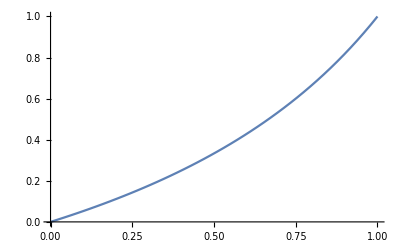

{{x→(K y)/(1+y)}}

```mathematica
Plot[x/(2-x),{x,0,1}]
Solve[x/(K-x)==y,x]
```

```mathematica
c1sol/.c3sol/.alphasubs//FullSimplify
Numerator[Subscript[c, 1]/.(c1sol/.c3sol)[[1]][[1]]/.alphasubs//Simplify]
x3bnd1=Solve[%==0,Subscript[ξ, 3]]//Factor
c3sol/.alphasubs//FullSimplify
```

{{{c_1→(c_2 ((ξ_1^2+α_1 (ξ_1-ξ_2)) (α_2+ξ_2)-α_1 ξ_2 ξ_3))/(ξ_2^3+α_2 ξ_2 (ξ_2-ξ_3))}}}

c_2 (ξ_1^2 (α_2+ξ_2)+α_1 (α_2 (ξ_1-ξ_2)-ξ_2 (-ξ_1+ξ_2+ξ_3)))

{{ξ_3→-((α_2+ξ_2) (-α_1 ξ_1-ξ_1^2+α_1 ξ_2))/(α_1 ξ_2)}}

{{c_3→(c_2 ξ_3^2)/(ξ_2^2+α_2 (ξ_2-ξ_3))}}

{A_1→3,A_2→3,A_3→2,B_1→4,B_2→2,ξ_1→1,ξ_2→0.5,ξ_3→0.2}

(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)

0.55

(ξ_1 (A_1+B_1+ξ_1))/(A_1+B_1)

8/7

1.14286

-((A_2+B_2+ξ_2) (-(A_1+B_1) ξ_1-ξ_1^2+(A_1+B_1) ξ_2))/((A_1+B_1) ξ_2)

7.07143

{{{c_1→27.4857 c_2}}}

{{c_3→0.0228571 c_2}}

{{c_3→(c_2 ξ_3^2)/(A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3)}}

{{17.556 (9.56173×10^-15-2.21714 s-0.214286 s^2+1. s^3) c_2}}

{{-(10.032 (9.56173×10^-15 c_2-2.21714 s c_2-0.214286 s^2 c_2+1. s^3 c_2))/s}}

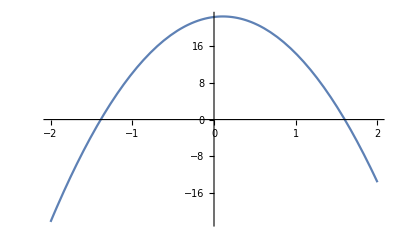

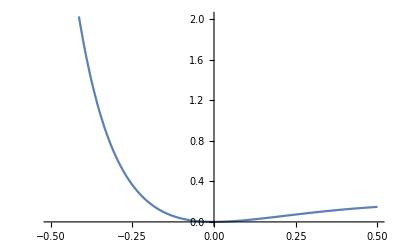

```mathematica
params={Subscript[A, 1]->3,Subscript[A, 2]->3,Subscript[A, 3]->2,Subscript[B, 1]->4,Subscript[B, 2]->2,Subscript[ξ, 1]->1,Subscript[ξ, 2]->0.5,Subscript[ξ, 3]->0.2}
X3bnd2=Subscript[ξ, 3]/. x3bnd2[[1]][[1]]
X3bnd2/.params//N
Subscript[ξ, 3]/.x3bnd2[[1]][[1]]/.{Subscript[A, 2]->Subscript[A, 1],Subscript[B, 2]->Subscript[B, 1],Subscript[ξ, 2]->Subscript[ξ, 1]}
%/.params
%//N
X3bnd1=Subscript[ξ, 3]/.x3bnd1[[1]]/.asubs
X3bnd1/.params//N
c1sol/.c3sol/.params
c3sol/.params
c3sol
(* sfun, dividing out a negative factor: *)Factor[sfun(-Subscript[A, 2] Subscript[ξ, 2]-Subscript[B, 2] Subscript[ξ, 2]-Subscript[ξ, 2]^2+Subscript[A, 2] Subscript[ξ, 3]+Subscript[B, 2] Subscript[ξ, 3])/.c1sol/.c3sol/.params] 
Factor[sfun/s/.c1sol/.c3sol/.params]
Plot[%/.Subscript[c, 2]->1,{s,-2,2}]
Plot[(Pt-Ps)/.c1sol/.c3sol/.Subscript[c, 2]->1/.params,{s,-0.5,0.5}]
(*Factor[sfun (-Subscript[A, 2] Subscript[ξ, 2]-Subscript[B, 2] Subscript[ξ, 2]-Subscript[ξ, 2]^2+Subscript[A, 2] Subscript[ξ, 3]+Subscript[B, 2] Subscript[ξ, 3])/.c1sol/.c3sol]*)
```

(x (x+a_1))/a_1

(y (y+a_2))/a_2

((x^2+(x+y) a_1) (y+a_2))/(a_1 (y+2 a_2))

{a_2→1,a_1→2}

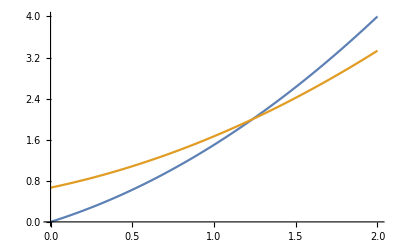

-Graphics3D-

```mathematica
eta1=x(Subscript[a, 1]+x)/Subscript[a, 1]
eta2 = y(Subscript[a, 2]+y)/Subscript[a, 2]
eta3=(Subscript[a, 2]+y)/(2 Subscript[a, 2]+y) (Subscript[a, 1](x+y)+x^2)/Subscript[a, 1]
as={Subscript[a, 2]->1,Subscript[a, 1]->2}
Plot[{eta1 /.{Subscript[a, 1]->2} , eta3/.{y->1,Subscript[a, 2]->1,Subscript[a, 1]->2},eta2/.{Subscript[a, 2]->1}},{x,0,2}]
Plot3D[{eta1/.as , eta2/.as, eta3/.as},{x,0,3},{y,0,3}]
```

```mathematica
bs[3]
```

```mathematica
bs[3]
```

-(A_1+ξ_1) (A_2+ξ_2) (A_3+ξ_3) (A_2 c_3+B_2 c_3+c_3 ξ_2+c_2 ξ_3)

```mathematica
bs0last=FactorList[bs[0]][[3]][[1]]
```

A_1 A_2 A_3 c_3 ξ_1 ξ_2+A_2 A_3 B_1 c_3 ξ_1 ξ_2+A_1 A_3 B_2 c_3 ξ_1 ξ_2+A_3 B_1 B_2 c_3 ξ_1 ξ_2+A_2 A_3 c_3 ξ_1^2 ξ_2+A_3 B_2 c_3 ξ_1^2 ξ_2+A_1 A_3 c_3 ξ_1 ξ_2^2+A_3 B_1 c_3 ξ_1 ξ_2^2+A_3 c_3 ξ_1^2 ξ_2^2+A_1 A_2^2 c_3 ξ_1 ξ_3+A_2^2 B_1 c_3 ξ_1 ξ_3+A_1 A_2 B_2 c_3 ξ_1 ξ_3+A_2 B_1 B_2 c_3 ξ_1 ξ_3+A_2^2 c_3 ξ_1^2 ξ_3+A_2 B_2 c_3 ξ_1^2 ξ_3-A_1 A_2^2 c_3 ξ_2 ξ_3-A_1 A_2 A_3 c_3 ξ_2 ξ_3-A_2^2 B_1 c_3 ξ_2 ξ_3-A_2 A_3 B_1 c_3 ξ_2 ξ_3-A_1 A_2 B_2 c_3 ξ_2 ξ_3-A_1 A_3 B_2 c_3 ξ_2 ξ_3-A_2 B_1 B_2 c_3 ξ_2 ξ_3-A_3 B_1 B_2 c_3 ξ_2 ξ_3+2 A_1 A_2 c_3 ξ_1 ξ_2 ξ_3+2 A_2 B_1 c_3 ξ_1 ξ_2 ξ_3+2 A_1 B_2 c_3 ξ_1 ξ_2 ξ_3+2 B_1 B_2 c_3 ξ_1 ξ_2 ξ_3+2 A_2 c_3 ξ_1^2 ξ_2 ξ_3+2 B_2 c_3 ξ_1^2 ξ_2 ξ_3-2 A_1 A_2 c_3 ξ_2^2 ξ_3-A_1 A_3 c_3 ξ_2^2 ξ_3-2 A_2 B_1 c_3 ξ_2^2 ξ_3-A_3 B_1 c_3 ξ_2^2 ξ_3-A_1 B_2 c_3 ξ_2^2 ξ_3-B_1 B_2 c_3 ξ_2^2 ξ_3+A_1 c_3 ξ_1 ξ_2^2 ξ_3+B_1 c_3 ξ_1 ξ_2^2 ξ_3+c_3 ξ_1^2 ξ_2^2 ξ_3-A_1 c_3 ξ_2^3 ξ_3-B_1 c_3 ξ_2^3 ξ_3+A_1 A_2 c_2 ξ_1 ξ_3^2+A_2 B_1 c_2 ξ_1 ξ_3^2+A_2 c_2 ξ_1^2 ξ_3^2-A_1 A_2 c_2 ξ_2 ξ_3^2-A_1 A_3 c_2 ξ_2 ξ_3^2-A_2 B_1 c_2 ξ_2 ξ_3^2-A_3 B_1 c_2 ξ_2 ξ_3^2-A_1 A_2 c_3 ξ_2 ξ_3^2-A_2 B_1 c_3 ξ_2 ξ_3^2-A_1 B_2 c_3 ξ_2 ξ_3^2-B_1 B_2 c_3 ξ_2 ξ_3^2+A_1 c_2 ξ_1 ξ_2 ξ_3^2+B_1 c_2 ξ_1 ξ_2 ξ_3^2+c_2 ξ_1^2 ξ_2 ξ_3^2-A_2 c_1 ξ_2^2 ξ_3^2-A_3 c_1 ξ_2^2 ξ_3^2-A_1 c_2 ξ_2^2 ξ_3^2-B_1 c_2 ξ_2^2 ξ_3^2-A_1 c_3 ξ_2^2 ξ_3^2-B_1 c_3 ξ_2^2 ξ_3^2-c_1 ξ_2^3 ξ_3^2-A_1 c_2 ξ_2 ξ_3^3-B_1 c_2 ξ_2 ξ_3^3-c_1 ξ_2^2 ξ_3^3

```mathematica
Factor[bs0last/.c1sol[[1]]/.alphasubs]
lastfactor0=FactorList[%][[5]][[1]]
Factor[bs0last/.c1sol[[1]]/.c3sol[[1]]/.alphasubs]
c3sol
```

ξ_1 (α_1+ξ_1) (B_2-α_2-ξ_2) (c_3 α_2 ξ_2+c_3 ξ_2^2-c_3 α_2 ξ_3-c_2 ξ_3^2)

c_3 α_2 ξ_2+c_3 ξ_2^2-c_3 α_2 ξ_3-c_2 ξ_3^2

0

{{c_3→(c_2 ξ_3^2)/(A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3)}}

```mathematica
bs1opt=Factor[bs[1]/.c1sol/.c3sol][[1]][[1]]
bs1optlast=FactorList[bs1opt][[6]][[1]]/.alphasubs//Factor
```

-((c_2 ξ_3 (A_1+A_2+A_3+ξ_1+ξ_2+ξ_3) (-A_1 A_2 A_3^2 ξ_1 ξ_2-A_2 A_3^2 B_1 ξ_1 ξ_2-A_1 A_3^2 B_2 ξ_1 ξ_2-A_3^2 B_1 B_2 ξ_1 ξ_2-A_2 A_3^2 ξ_1^2 ξ_2-A_3^2 B_2 ξ_1^2 ξ_2-A_1 A_3^2 ξ_1 ξ_2^2-A_3^2 B_1 ξ_1 ξ_2^2-A_3^2 ξ_1^2 ξ_2^2-A_1 A_2^3 ξ_1 ξ_3-A_1 A_2^2 A_3 ξ_1 ξ_3-A_2^3 B_1 ξ_1 ξ_3-A_2^2 A_3 B_1 ξ_1 ξ_3-A_1 A_2^2 B_2 ξ_1 ξ_3-A_1 A_2 A_3 B_2 ξ_1 ξ_3-A_2^2 B_1 B_2 ξ_1 ξ_3-A_2 A_3 B_1 B_2 ξ_1 ξ_3-A_2^3 ξ_1^2 ξ_3-A_2^2 A_3 ξ_1^2 ξ_3-A_2^2 B_2 ξ_1^2 ξ_3-A_2 A_3 B_2 ξ_1^2 ξ_3+A_1^2 A_2^2 ξ_2 ξ_3+A_1 A_2^3 ξ_2 ξ_3+A_1^2 A_2 A_3 ξ_2 ξ_3+2 A_1 A_2^2 A_3 ξ_2 ξ_3+A_1 A_2 A_3^2 ξ_2 ξ_3+A_1 A_2^2 B_1 ξ_2 ξ_3+A_2^3 B_1 ξ_2 ξ_3+A_1 A_2 A_3 B_1 ξ_2 ξ_3+2 A_2^2 A_3 B_1 ξ_2 ξ_3+A_2 A_3^2 B_1 ξ_2 ξ_3+A_1^2 A_2 B_2 ξ_2 ξ_3+A_1 A_2^2 B_2 ξ_2 ξ_3+A_1^2 A_3 B_2 ξ_2 ξ_3+2 A_1 A_2 A_3 B_2 ξ_2 ξ_3+A_1 A_3^2 B_2 ξ_2 ξ_3+A_1 A_2 B_1 B_2 ξ_2 ξ_3+A_2^2 B_1 B_2 ξ_2 ξ_3+A_1 A_3 B_1 B_2 ξ_2 ξ_3+2 A_2 A_3 B_1 B_2 ξ_2 ξ_3+A_3^2 B_1 B_2 ξ_2 ξ_3+A_2^3 ξ_1 ξ_2 ξ_3+2 A_2^2 A_3 ξ_1 ξ_2 ξ_3+A_2 A_3^2 ξ_1 ξ_2 ξ_3-2 A_2^2 B_1 ξ_1 ξ_2 ξ_3-2 A_2 A_3 B_1 ξ_1 ξ_2 ξ_3+A_1 A_2 B_2 ξ_1 ξ_2 ξ_3+A_2^2 B_2 ξ_1 ξ_2 ξ_3+2 A_2 A_3 B_2 ξ_1 ξ_2 ξ_3+A_3^2 B_2 ξ_1 ξ_2 ξ_3-A_2 B_1 B_2 ξ_1 ξ_2 ξ_3-2 A_3 B_1 B_2 ξ_1 ξ_2 ξ_3-A_2^2 ξ_1^2 ξ_2 ξ_3-A_2 A_3 ξ_1^2 ξ_2 ξ_3-A_3 B_2 ξ_1^2 ξ_2 ξ_3+2 A_1^2 A_2 ξ_2^2 ξ_3+3 A_1 A_2^2 ξ_2^2 ξ_3+A_1^2 A_3 ξ_2^2 ξ_3+4 A_1 A_2 A_3 ξ_2^2 ξ_3+A_1 A_3^2 ξ_2^2 ξ_3+2 A_1 A_2 B_1 ξ_2^2 ξ_3+3 A_2^2 B_1 ξ_2^2 ξ_3+A_1 A_3 B_1 ξ_2^2 ξ_3+4 A_2 A_3 B_1 ξ_2^2 ξ_3+A_3^2 B_1 ξ_2^2 ξ_3+A_1^2 B_2 ξ_2^2 ξ_3+2 A_1 A_2 B_2 ξ_2^2 ξ_3+2 A_1 A_3 B_2 ξ_2^2 ξ_3+A_1 B_1 B_2 ξ_2^2 ξ_3+2 A_2 B_1 B_2 ξ_2^2 ξ_3+2 A_3 B_1 B_2 ξ_2^2 ξ_3+3 A_1 A_2 ξ_1 ξ_2^2 ξ_3+3 A_2^2 ξ_1 ξ_2^2 ξ_3+A_1 A_3 ξ_1 ξ_2^2 ξ_3+4 A_2 A_3 ξ_1 ξ_2^2 ξ_3+A_3^2 ξ_1 ξ_2^2 ξ_3-A_2 B_1 ξ_1 ξ_2^2 ξ_3-A_3 B_1 ξ_1 ξ_2^2 ξ_3+2 A_1 B_2 ξ_1 ξ_2^2 ξ_3+2 A_2 B_2 ξ_1 ξ_2^2 ξ_3+2 A_3 B_2 ξ_1 ξ_2^2 ξ_3+A_2 ξ_1^2 ξ_2^2 ξ_3+B_2 ξ_1^2 ξ_2^2 ξ_3+A_1^2 ξ_2^3 ξ_3+3 A_1 A_2 ξ_2^3 ξ_3+2 A_1 A_3 ξ_2^3 ξ_3+A_1 B_1 ξ_2^3 ξ_3+3 A_2 B_1 ξ_2^3 ξ_3+2 A_3 B_1 ξ_2^3 ξ_3+A_1 B_2 ξ_2^3 ξ_3+B_1 B_2 ξ_2^3 ξ_3+2 A_1 ξ_1 ξ_2^3 ξ_3+3 A_2 ξ_1 ξ_2^3 ξ_3+2 A_3 ξ_1 ξ_2^3 ξ_3+B_2 ξ_1 ξ_2^3 ξ_3+ξ_1^2 ξ_2^3 ξ_3+A_1 ξ_2^4 ξ_3+B_1 ξ_2^4 ξ_3+ξ_1 ξ_2^4 ξ_3-A_1 A_2^2 ξ_1 ξ_3^2-A_2^2 B_1 ξ_1 ξ_3^2-A_1 A_2 B_2 ξ_1 ξ_3^2-A_2 B_1 B_2 ξ_1 ξ_3^2-A_2^2 ξ_1^2 ξ_3^2-A_2 B_2 ξ_1^2 ξ_3^2+A_1^2 A_2 ξ_2 ξ_3^2+2 A_1 A_2^2 ξ_2 ξ_3^2+2 A_1 A_2 A_3 ξ_2 ξ_3^2+A_1 A_2 B_1 ξ_2 ξ_3^2+2 A_2^2 B_1 ξ_2 ξ_3^2+2 A_2 A_3 B_1 ξ_2 ξ_3^2+A_1^2 B_2 ξ_2 ξ_3^2+2 A_1 A_2 B_2 ξ_2 ξ_3^2+2 A_1 A_3 B_2 ξ_2 ξ_3^2+A_1 B_1 B_2 ξ_2 ξ_3^2+2 A_2 B_1 B_2 ξ_2 ξ_3^2+2 A_3 B_1 B_2 ξ_2 ξ_3^2+A_1 A_2 ξ_1 ξ_2 ξ_3^2+2 A_2^2 ξ_1 ξ_2 ξ_3^2+2 A_2 A_3 ξ_1 ξ_2 ξ_3^2-A_2 B_1 ξ_1 ξ_2 ξ_3^2+A_1 B_2 ξ_1 ξ_2 ξ_3^2+2 A_2 B_2 ξ_1 ξ_2 ξ_3^2+2 A_3 B_2 ξ_1 ξ_2 ξ_3^2-B_1 B_2 ξ_1 ξ_2 ξ_3^2+A_1^2 ξ_2^2 ξ_3^2+4 A_1 A_2 ξ_2^2 ξ_3^2+2 A_1 A_3 ξ_2^2 ξ_3^2+A_1 B_1 ξ_2^2 ξ_3^2+4 A_2 B_1 ξ_2^2 ξ_3^2+2 A_3 B_1 ξ_2^2 ξ_3^2+2 A_1 B_2 ξ_2^2 ξ_3^2+2 B_1 B_2 ξ_2^2 ξ_3^2+2 A_1 ξ_1 ξ_2^2 ξ_3^2+4 A_2 ξ_1 ξ_2^2 ξ_3^2+2 A_3 ξ_1 ξ_2^2 ξ_3^2+2 B_2 ξ_1 ξ_2^2 ξ_3^2+ξ_1^2 ξ_2^2 ξ_3^2+2 A_1 ξ_2^3 ξ_3^2+2 B_1 ξ_2^3 ξ_3^2+2 ξ_1 ξ_2^3 ξ_3^2+A_1 A_2 ξ_2 ξ_3^3+A_2 B_1 ξ_2 ξ_3^3+A_1 B_2 ξ_2 ξ_3^3+B_1 B_2 ξ_2 ξ_3^3+A_2 ξ_1 ξ_2 ξ_3^3+B_2 ξ_1 ξ_2 ξ_3^3+A_1 ξ_2^2 ξ_3^3+B_1 ξ_2^2 ξ_3^3+ξ_1 ξ_2^2 ξ_3^3))/(A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3))

-A_3^2 α_1 α_2 ξ_1 ξ_2-A_3^2 α_2 ξ_1^2 ξ_2-A_3^2 α_1 ξ_1 ξ_2^2-A_3^2 ξ_1^2 ξ_2^2+A_3 B_2 α_1 α_2 ξ_1 ξ_3-B_2^2 α_1 α_2 ξ_1 ξ_3-A_3 α_1 α_2^2 ξ_1 ξ_3+2 B_2 α_1 α_2^2 ξ_1 ξ_3-α_1 α_2^3 ξ_1 ξ_3+A_3 B_2 α_2 ξ_1^2 ξ_3-B_2^2 α_2 ξ_1^2 ξ_3-A_3 α_2^2 ξ_1^2 ξ_3+2 B_2 α_2^2 ξ_1^2 ξ_3-α_2^3 ξ_1^2 ξ_3+A_3^2 α_1 α_2 ξ_2 ξ_3-A_3 B_1 α_1 α_2 ξ_2 ξ_3-2 A_3 B_2 α_1 α_2 ξ_2 ξ_3+B_1 B_2 α_1 α_2 ξ_2 ξ_3+B_2^2 α_1 α_2 ξ_2 ξ_3+A_3 α_1^2 α_2 ξ_2 ξ_3-B_2 α_1^2 α_2 ξ_2 ξ_3+2 A_3 α_1 α_2^2 ξ_2 ξ_3-B_1 α_1 α_2^2 ξ_2 ξ_3-2 B_2 α_1 α_2^2 ξ_2 ξ_3+α_1^2 α_2^2 ξ_2 ξ_3+α_1 α_2^3 ξ_2 ξ_3-B_2^2 α_1 ξ_1 ξ_2 ξ_3+A_3^2 α_2 ξ_1 ξ_2 ξ_3-2 A_3 B_1 α_2 ξ_1 ξ_2 ξ_3-2 A_3 B_2 α_2 ξ_1 ξ_2 ξ_3+2 B_1 B_2 α_2 ξ_1 ξ_2 ξ_3+B_2^2 α_2 ξ_1 ξ_2 ξ_3+B_2 α_1 α_2 ξ_1 ξ_2 ξ_3+2 A_3 α_2^2 ξ_1 ξ_2 ξ_3-2 B_1 α_2^2 ξ_1 ξ_2 ξ_3-2 B_2 α_2^2 ξ_1 ξ_2 ξ_3+α_2^3 ξ_1 ξ_2 ξ_3-B_2^2 ξ_1^2 ξ_2 ξ_3-A_3 α_2 ξ_1^2 ξ_2 ξ_3+2 B_2 α_2 ξ_1^2 ξ_2 ξ_3-α_2^2 ξ_1^2 ξ_2 ξ_3+A_3^2 α_1 ξ_2^2 ξ_3-A_3 B_1 α_1 ξ_2^2 ξ_3-2 A_3 B_2 α_1 ξ_2^2 ξ_3+B_1 B_2 α_1 ξ_2^2 ξ_3+B_2^2 α_1 ξ_2^2 ξ_3+A_3 α_1^2 ξ_2^2 ξ_3-B_2 α_1^2 ξ_2^2 ξ_3+4 A_3 α_1 α_2 ξ_2^2 ξ_3-2 B_1 α_1 α_2 ξ_2^2 ξ_3-4 B_2 α_1 α_2 ξ_2^2 ξ_3+2 α_1^2 α_2 ξ_2^2 ξ_3+3 α_1 α_2^2 ξ_2^2 ξ_3+A_3^2 ξ_1 ξ_2^2 ξ_3-2 A_3 B_1 ξ_1 ξ_2^2 ξ_3-2 A_3 B_2 ξ_1 ξ_2^2 ξ_3+2 B_1 B_2 ξ_1 ξ_2^2 ξ_3+B_2^2 ξ_1 ξ_2^2 ξ_3+A_3 α_1 ξ_1 ξ_2^2 ξ_3-B_2 α_1 ξ_1 ξ_2^2 ξ_3+4 A_3 α_2 ξ_1 ξ_2^2 ξ_3-4 B_1 α_2 ξ_1 ξ_2^2 ξ_3-4 B_2 α_2 ξ_1 ξ_2^2 ξ_3+3 α_1 α_2 ξ_1 ξ_2^2 ξ_3+3 α_2^2 ξ_1 ξ_2^2 ξ_3+α_2 ξ_1^2 ξ_2^2 ξ_3+2 A_3 α_1 ξ_2^3 ξ_3-B_1 α_1 ξ_2^3 ξ_3-2 B_2 α_1 ξ_2^3 ξ_3+α_1^2 ξ_2^3 ξ_3+3 α_1 α_2 ξ_2^3 ξ_3+2 A_3 ξ_1 ξ_2^3 ξ_3-2 B_1 ξ_1 ξ_2^3 ξ_3-2 B_2 ξ_1 ξ_2^3 ξ_3+2 α_1 ξ_1 ξ_2^3 ξ_3+3 α_2 ξ_1 ξ_2^3 ξ_3+ξ_1^2 ξ_2^3 ξ_3+α_1 ξ_2^4 ξ_3+ξ_1 ξ_2^4 ξ_3+B_2 α_1 α_2 ξ_1 ξ_3^2-α_1 α_2^2 ξ_1 ξ_3^2+B_2 α_2 ξ_1^2 ξ_3^2-α_2^2 ξ_1^2 ξ_3^2+2 A_3 α_1 α_2 ξ_2 ξ_3^2-B_1 α_1 α_2 ξ_2 ξ_3^2-2 B_2 α_1 α_2 ξ_2 ξ_3^2+α_1^2 α_2 ξ_2 ξ_3^2+2 α_1 α_2^2 ξ_2 ξ_3^2+2 A_3 α_2 ξ_1 ξ_2 ξ_3^2-2 B_1 α_2 ξ_1 ξ_2 ξ_3^2-2 B_2 α_2 ξ_1 ξ_2 ξ_3^2+α_1 α_2 ξ_1 ξ_2 ξ_3^2+2 α_2^2 ξ_1 ξ_2 ξ_3^2+2 A_3 α_1 ξ_2^2 ξ_3^2-B_1 α_1 ξ_2^2 ξ_3^2-2 B_2 α_1 ξ_2^2 ξ_3^2+α_1^2 ξ_2^2 ξ_3^2+4 α_1 α_2 ξ_2^2 ξ_3^2+2 A_3 ξ_1 ξ_2^2 ξ_3^2-2 B_1 ξ_1 ξ_2^2 ξ_3^2-2 B_2 ξ_1 ξ_2^2 ξ_3^2+2 α_1 ξ_1 ξ_2^2 ξ_3^2+4 α_2 ξ_1 ξ_2^2 ξ_3^2+ξ_1^2 ξ_2^2 ξ_3^2+2 α_1 ξ_2^3 ξ_3^2+2 ξ_1 ξ_2^3 ξ_3^2+α_1 α_2 ξ_2 ξ_3^3+α_2 ξ_1 ξ_2 ξ_3^3+α_1 ξ_2^2 ξ_3^3+ξ_1 ξ_2^2 ξ_3^3

```mathematica
X3bnd2=Subscript[ξ, 3]/. x3bnd1[[1]][[1]]/.alphasubs
X3bnd1=X3bnd2/.{Subscript[ξ, 2]->Subscript[ξ, 1],Subscript[α, 2]->Subscript[α, 1]}
Collect[bs1optlast,Subscript[ξ, 3],Factor]
bs1optpromising=Collect[bs1optlast,Subscript[ξ, 3],FullSimplify]
Collect[bs1optlast/.asubs/.xix,Subscript[x, 3],FullSimplify]
FullSimplify[bs1optlast/.asubs/.xix]
(*Factor[Collect[bs1optlast,Subscript[ξ, 3],Factor]/.{Subscript[ξ, 3]->(X3bnd2)}]*)
```

(ξ_2 (α_2+ξ_2))/α_2

(ξ_1 (α_1+ξ_1))/α_1

-A_3^2 ξ_1 (α_1+ξ_1) ξ_2 (α_2+ξ_2)+(A_3 B_2 α_1 α_2 ξ_1-B_2^2 α_1 α_2 ξ_1-A_3 α_1 α_2^2 ξ_1+2 B_2 α_1 α_2^2 ξ_1-α_1 α_2^3 ξ_1+A_3 B_2 α_2 ξ_1^2-B_2^2 α_2 ξ_1^2-A_3 α_2^2 ξ_1^2+2 B_2 α_2^2 ξ_1^2-α_2^3 ξ_1^2+A_3^2 α_1 α_2 ξ_2-A_3 B_1 α_1 α_2 ξ_2-2 A_3 B_2 α_1 α_2 ξ_2+B_1 B_2 α_1 α_2 ξ_2+B_2^2 α_1 α_2 ξ_2+A_3 α_1^2 α_2 ξ_2-B_2 α_1^2 α_2 ξ_2+2 A_3 α_1 α_2^2 ξ_2-B_1 α_1 α_2^2 ξ_2-2 B_2 α_1 α_2^2 ξ_2+α_1^2 α_2^2 ξ_2+α_1 α_2^3 ξ_2-B_2^2 α_1 ξ_1 ξ_2+A_3^2 α_2 ξ_1 ξ_2-2 A_3 B_1 α_2 ξ_1 ξ_2-2 A_3 B_2 α_2 ξ_1 ξ_2+2 B_1 B_2 α_2 ξ_1 ξ_2+B_2^2 α_2 ξ_1 ξ_2+B_2 α_1 α_2 ξ_1 ξ_2+2 A_3 α_2^2 ξ_1 ξ_2-2 B_1 α_2^2 ξ_1 ξ_2-2 B_2 α_2^2 ξ_1 ξ_2+α_2^3 ξ_1 ξ_2-B_2^2 ξ_1^2 ξ_2-A_3 α_2 ξ_1^2 ξ_2+2 B_2 α_2 ξ_1^2 ξ_2-α_2^2 ξ_1^2 ξ_2+A_3^2 α_1 ξ_2^2-A_3 B_1 α_1 ξ_2^2-2 A_3 B_2 α_1 ξ_2^2+B_1 B_2 α_1 ξ_2^2+B_2^2 α_1 ξ_2^2+A_3 α_1^2 ξ_2^2-B_2 α_1^2 ξ_2^2+4 A_3 α_1 α_2 ξ_2^2-2 B_1 α_1 α_2 ξ_2^2-4 B_2 α_1 α_2 ξ_2^2+2 α_1^2 α_2 ξ_2^2+3 α_1 α_2^2 ξ_2^2+A_3^2 ξ_1 ξ_2^2-2 A_3 B_1 ξ_1 ξ_2^2-2 A_3 B_2 ξ_1 ξ_2^2+2 B_1 B_2 ξ_1 ξ_2^2+B_2^2 ξ_1 ξ_2^2+A_3 α_1 ξ_1 ξ_2^2-B_2 α_1 ξ_1 ξ_2^2+4 A_3 α_2 ξ_1 ξ_2^2-4 B_1 α_2 ξ_1 ξ_2^2-4 B_2 α_2 ξ_1 ξ_2^2+3 α_1 α_2 ξ_1 ξ_2^2+3 α_2^2 ξ_1 ξ_2^2+α_2 ξ_1^2 ξ_2^2+2 A_3 α_1 ξ_2^3-B_1 α_1 ξ_2^3-2 B_2 α_1 ξ_2^3+α_1^2 ξ_2^3+3 α_1 α_2 ξ_2^3+2 A_3 ξ_1 ξ_2^3-2 B_1 ξ_1 ξ_2^3-2 B_2 ξ_1 ξ_2^3+2 α_1 ξ_1 ξ_2^3+3 α_2 ξ_1 ξ_2^3+ξ_1^2 ξ_2^3+α_1 ξ_2^4+ξ_1 ξ_2^4) ξ_3+(B_2 α_1 α_2 ξ_1-α_1 α_2^2 ξ_1+B_2 α_2 ξ_1^2-α_2^2 ξ_1^2+2 A_3 α_1 α_2 ξ_2-B_1 α_1 α_2 ξ_2-2 B_2 α_1 α_2 ξ_2+α_1^2 α_2 ξ_2+2 α_1 α_2^2 ξ_2+2 A_3 α_2 ξ_1 ξ_2-2 B_1 α_2 ξ_1 ξ_2-2 B_2 α_2 ξ_1 ξ_2+α_1 α_2 ξ_1 ξ_2+2 α_2^2 ξ_1 ξ_2+2 A_3 α_1 ξ_2^2-B_1 α_1 ξ_2^2-2 B_2 α_1 ξ_2^2+α_1^2 ξ_2^2+4 α_1 α_2 ξ_2^2+2 A_3 ξ_1 ξ_2^2-2 B_1 ξ_1 ξ_2^2-2 B_2 ξ_1 ξ_2^2+2 α_1 ξ_1 ξ_2^2+4 α_2 ξ_1 ξ_2^2+ξ_1^2 ξ_2^2+2 α_1 ξ_2^3+2 ξ_1 ξ_2^3) ξ_3^2+(α_1+ξ_1) ξ_2 (α_2+ξ_2) ξ_3^3

-A_3^2 ξ_1 (α_1+ξ_1) ξ_2 (α_2+ξ_2)+(A_3^2 (α_1+ξ_1) ξ_2 (α_2+ξ_2)-(B_2-α_2-ξ_2) (α_2+ξ_2) ((B_2-α_2) ξ_1 (α_1+ξ_1)+(-(B_2-α_1-α_2-ξ_1) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+(α_1+ξ_1) ξ_2^2)+A_3 (B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+((α_1+2 α_2) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2))) ξ_3+(B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+(2 A_3 (α_1+ξ_1)+(α_1+ξ_1) (α_1+2 α_2+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2)) ξ_3^2+(α_1+ξ_1) ξ_2 (α_2+ξ_2) ξ_3^3

-A_3 x_2 (B_2+x_2) (A_1 (A_2 x_1+B_1 x_2)+x_2 (x_1^2+(B_1+x_1) x_2)-A_2 (x_1 (B_1+2 x_1)+(B_1+x_1) x_2))+(A_2 (A_3 (B_2 x_1 (B_1+2 x_1)+(2 B_1 (B_2+x_1)+x_1 (2 B_2+3 x_1)) x_2+2 (B_1+x_1) x_2^2)-x_2 (B_2+x_2) (B_1 (x_1+x_2)+x_1 (2 x_1+x_2)))+A_1 (x_2 (B_1 x_2 (B_2+x_2)+A_3 (-B_1 B_2+x_1 x_2))+A_2 (x_1 x_2 (B_2+x_2)-A_3 (B_2 x_1+(B_1+2 x_1) x_2)))+x_2 (x_2 (B_2+x_2) (x_1^2+(B_1+x_1) x_2)-A_3 (B_2 (x_1^2+2 (B_1+x_1) x_2)+x_2 (2 x_1 (x_1+x_2)+B_1 (x_1+2 x_2))))) x_3+(x_2 (-A_3 (B_1+x_1) (B_2+x_2)+x_1 x_2 (2 B_2+x_1+2 x_2)+B_1 (-B_2 (x_1-2 x_2)+2 x_2^2))+A_1 (A_2 (-B_1 B_2+x_1 x_2)+x_2 (B_2 x_1+B_1 (2 B_2+x_2)))+A_2 (A_3 (B_1+x_1) (B_2+x_2)-B_2 (x_1^2+2 (B_1+x_1) x_2)-x_2 (2 x_1 (x_1+x_2)+B_1 (x_1+2 x_2)))) x_3^2-(B_1+x_1) (A_2-x_2) (B_2+x_2) x_3^3

A_1 (A_2 (x_3 (x_1 x_2 (B_2+x_2)+(-B_1 B_2+x_1 x_2) x_3)+A_3 (-x_1 x_2 (B_2+x_2)-(B_2 x_1+(B_1+2 x_1) x_2) x_3))+x_2 (x_3 (B_2 x_1 x_3+B_1 (x_2 (B_2+x_2)+(2 B_2+x_2) x_3))+A_3 (x_1 x_2 x_3-B_1 (x_2^2+B_2 (x_2+x_3)))))-x_2 (-x_3 (x_2 (x_2+x_3) (B_1 (x_2+x_3)+x_1 (x_1+x_2+x_3))+B_2 (x_1^2 x_2+B_1 (x_2+x_3)^2+x_1 (-B_1 x_3+(x_2+x_3)^2)))+A_3 (B_2 (x_2+x_3) (B_1 (x_2+x_3)+x_1 (x_1+x_2+x_3))+x_2 (B_1 (x_2+x_3)^2+x_1^2 (x_2+2 x_3)+x_1 (B_1 x_3+(x_2+x_3)^2))))+A_2 (-x_3 (B_1 (x_2 (x_2+x_3) (x_1+x_2+x_3)+B_2 (x_1 x_2+(x_2+x_3)^2))+x_1 (x_2 (x_2+x_3) (2 x_1+x_2+x_3)+B_2 ((x_2+x_3)^2+x_1 (2 x_2+x_3))))+A_3 (B_1 (B_2 (x_2+x_3) (x_1+x_2+x_3)+x_2 ((x_2+x_3)^2+x_1 (x_2+2 x_3)))+x_1 (B_2 (x_2+x_3) (2 x_1+x_2+x_3)+x_2 ((x_2+x_3)^2+x_1 (2 x_2+3 x_3)))))

```mathematica
bs2opt=Factor[bs[2]/.c1sol/.c3sol/.alphasubs][[1]][[1]]
bs2optlast=FactorList[bs2opt][[5]][[1]];
Collect[bs2optlast,Subscript[ξ, 3],FullSimplify]
Collect[bs2optlast/.asubs/.xix,Subscript[x, 3],FullSimplify]
Collect[bs2optlast/.asubs/.xix/.alphasubs,Subscript[x, 3],FullSimplify]
```

-1/(-α_2 ξ_2-ξ_2^2+α_2 ξ_3)c_2 ξ_3 (-A_3^2 B_2 α_1 α_2 ξ_1+A_3 B_2^2 α_1 α_2 ξ_1+A_3^2 α_1 α_2^2 ξ_1-2 A_3 B_2 α_1 α_2^2 ξ_1+A_3 α_1 α_2^3 ξ_1-A_3^2 B_2 α_2 ξ_1^2+A_3 B_2^2 α_2 ξ_1^2+A_3^2 α_2^2 ξ_1^2-2 A_3 B_2 α_2^2 ξ_1^2+A_3 α_2^3 ξ_1^2+A_3^2 B_2 α_1 α_2 ξ_2-A_3 B_1 B_2 α_1 α_2 ξ_2-A_3 B_2^2 α_1 α_2 ξ_2+A_3 B_2 α_1^2 α_2 ξ_2-A_3^2 α_1 α_2^2 ξ_2+A_3 B_1 α_1 α_2^2 ξ_2+2 A_3 B_2 α_1 α_2^2 ξ_2-A_3 α_1^2 α_2^2 ξ_2-A_3 α_1 α_2^3 ξ_2-A_3^2 B_2 α_1 ξ_1 ξ_2+A_3 B_2^2 α_1 ξ_1 ξ_2+A_3^2 B_2 α_2 ξ_1 ξ_2-2 A_3 B_1 B_2 α_2 ξ_1 ξ_2-A_3 B_2^2 α_2 ξ_1 ξ_2+2 A_3^2 α_1 α_2 ξ_1 ξ_2-A_3 B_2 α_1 α_2 ξ_1 ξ_2-A_3^2 α_2^2 ξ_1 ξ_2+2 A_3 B_1 α_2^2 ξ_1 ξ_2+2 A_3 B_2 α_2^2 ξ_1 ξ_2-A_3 α_2^3 ξ_1 ξ_2-A_3^2 B_2 ξ_1^2 ξ_2+A_3 B_2^2 ξ_1^2 ξ_2+2 A_3^2 α_2 ξ_1^2 ξ_2-2 A_3 B_2 α_2 ξ_1^2 ξ_2+A_3 α_2^2 ξ_1^2 ξ_2+A_3^2 B_2 α_1 ξ_2^2-A_3 B_1 B_2 α_1 ξ_2^2-A_3 B_2^2 α_1 ξ_2^2+A_3 B_2 α_1^2 ξ_2^2-2 A_3^2 α_1 α_2 ξ_2^2+2 A_3 B_1 α_1 α_2 ξ_2^2+4 A_3 B_2 α_1 α_2 ξ_2^2-2 A_3 α_1^2 α_2 ξ_2^2-3 A_3 α_1 α_2^2 ξ_2^2+A_3^2 B_2 ξ_1 ξ_2^2-2 A_3 B_1 B_2 ξ_1 ξ_2^2-A_3 B_2^2 ξ_1 ξ_2^2+A_3^2 α_1 ξ_1 ξ_2^2+A_3 B_2 α_1 ξ_1 ξ_2^2-2 A_3^2 α_2 ξ_1 ξ_2^2+4 A_3 B_1 α_2 ξ_1 ξ_2^2+4 A_3 B_2 α_2 ξ_1 ξ_2^2-3 A_3 α_1 α_2 ξ_1 ξ_2^2-3 A_3 α_2^2 ξ_1 ξ_2^2+A_3^2 ξ_1^2 ξ_2^2-A_3 α_2 ξ_1^2 ξ_2^2-A_3^2 α_1 ξ_2^3+A_3 B_1 α_1 ξ_2^3+2 A_3 B_2 α_1 ξ_2^3-A_3 α_1^2 ξ_2^3-3 A_3 α_1 α_2 ξ_2^3-A_3^2 ξ_1 ξ_2^3+2 A_3 B_1 ξ_1 ξ_2^3+2 A_3 B_2 ξ_1 ξ_2^3-2 A_3 α_1 ξ_1 ξ_2^3-3 A_3 α_2 ξ_1 ξ_2^3-A_3 ξ_1^2 ξ_2^3-A_3 α_1 ξ_2^4-A_3 ξ_1 ξ_2^4-2 A_3 B_2 α_1 α_2 ξ_1 ξ_3+B_2^2 α_1 α_2 ξ_1 ξ_3+2 A_3 α_1 α_2^2 ξ_1 ξ_3-2 B_2 α_1 α_2^2 ξ_1 ξ_3+α_1 α_2^3 ξ_1 ξ_3-2 A_3 B_2 α_2 ξ_1^2 ξ_3+B_2^2 α_2 ξ_1^2 ξ_3+2 A_3 α_2^2 ξ_1^2 ξ_3-2 B_2 α_2^2 ξ_1^2 ξ_3+α_2^3 ξ_1^2 ξ_3+A_3^2 B_2 α_1 ξ_2 ξ_3-A_3 B_1 B_2 α_1 ξ_2 ξ_3-A_3 B_2^2 α_1 ξ_2 ξ_3+A_3 B_2 α_1^2 ξ_2 ξ_3+A_3^2 B_1 α_2 ξ_2 ξ_3-A_3 B_1^2 α_2 ξ_2 ξ_3-2 A_3 B_1 B_2 α_2 ξ_2 ξ_3+B_1^2 B_2 α_2 ξ_2 ξ_3+B_1 B_2^2 α_2 ξ_2 ξ_3-2 A_3^2 α_1 α_2 ξ_2 ξ_3+3 A_3 B_1 α_1 α_2 ξ_2 ξ_3+6 A_3 B_2 α_1 α_2 ξ_2 ξ_3-3 B_1 B_2 α_1 α_2 ξ_2 ξ_3-2 B_2^2 α_1 α_2 ξ_2 ξ_3-2 A_3 α_1^2 α_2 ξ_2 ξ_3+2 B_2 α_1^2 α_2 ξ_2 ξ_3+2 A_3 B_1 α_2^2 ξ_2 ξ_3-B_1^2 α_2^2 ξ_2 ξ_3-2 B_1 B_2 α_2^2 ξ_2 ξ_3-5 A_3 α_1 α_2^2 ξ_2 ξ_3+3 B_1 α_1 α_2^2 ξ_2 ξ_3+4 B_2 α_1 α_2^2 ξ_2 ξ_3-2 α_1^2 α_2^2 ξ_2 ξ_3+B_1 α_2^3 ξ_2 ξ_3-2 α_1 α_2^3 ξ_2 ξ_3+A_3^2 B_2 ξ_1 ξ_2 ξ_3-2 A_3 B_1 B_2 ξ_1 ξ_2 ξ_3-A_3 B_2^2 ξ_1 ξ_2 ξ_3+A_3 B_2 α_1 ξ_1 ξ_2 ξ_3+B_2^2 α_1 ξ_1 ξ_2 ξ_3-2 A_3^2 α_2 ξ_1 ξ_2 ξ_3+4 A_3 B_1 α_2 ξ_1 ξ_2 ξ_3+6 A_3 B_2 α_2 ξ_1 ξ_2 ξ_3-4 B_1 B_2 α_2 ξ_1 ξ_2 ξ_3-2 B_2^2 α_2 ξ_1 ξ_2 ξ_3-A_3 α_1 α_2 ξ_1 ξ_2 ξ_3+B_2 α_1 α_2 ξ_1 ξ_2 ξ_3-5 A_3 α_2^2 ξ_1 ξ_2 ξ_3+4 B_1 α_2^2 ξ_1 ξ_2 ξ_3+4 B_2 α_2^2 ξ_1 ξ_2 ξ_3-2 α_1 α_2^2 ξ_1 ξ_2 ξ_3-2 α_2^3 ξ_1 ξ_2 ξ_3+B_2^2 ξ_1^2 ξ_2 ξ_3+A_3 α_2 ξ_1^2 ξ_2 ξ_3-B_2 α_2 ξ_1^2 ξ_2 ξ_3+A_3^2 B_1 ξ_2^2 ξ_3-A_3 B_1^2 ξ_2^2 ξ_3-2 A_3 B_1 B_2 ξ_2^2 ξ_3+B_1^2 B_2 ξ_2^2 ξ_3+B_1 B_2^2 ξ_2^2 ξ_3-2 A_3^2 α_1 ξ_2^2 ξ_3+3 A_3 B_1 α_1 ξ_2^2 ξ_3+6 A_3 B_2 α_1 ξ_2^2 ξ_3-3 B_1 B_2 α_1 ξ_2^2 ξ_3-2 B_2^2 α_1 ξ_2^2 ξ_3-2 A_3 α_1^2 ξ_2^2 ξ_3+2 B_2 α_1^2 ξ_2^2 ξ_3+4 A_3 B_1 α_2 ξ_2^2 ξ_3-2 B_1^2 α_2 ξ_2^2 ξ_3-4 B_1 B_2 α_2 ξ_2^2 ξ_3-10 A_3 α_1 α_2 ξ_2^2 ξ_3+6 B_1 α_1 α_2 ξ_2^2 ξ_3+8 B_2 α_1 α_2 ξ_2^2 ξ_3-4 α_1^2 α_2 ξ_2^2 ξ_3+3 B_1 α_2^2 ξ_2^2 ξ_3-6 α_1 α_2^2 ξ_2^2 ξ_3-2 A_3^2 ξ_1 ξ_2^2 ξ_3+4 A_3 B_1 ξ_1 ξ_2^2 ξ_3+6 A_3 B_2 ξ_1 ξ_2^2 ξ_3-4 B_1 B_2 ξ_1 ξ_2^2 ξ_3-2 B_2^2 ξ_1 ξ_2^2 ξ_3-3 A_3 α_1 ξ_1 ξ_2^2 ξ_3+3 B_2 α_1 ξ_1 ξ_2^2 ξ_3-10 A_3 α_2 ξ_1 ξ_2^2 ξ_3+8 B_1 α_2 ξ_1 ξ_2^2 ξ_3+8 B_2 α_2 ξ_1 ξ_2^2 ξ_3-7 α_1 α_2 ξ_1 ξ_2^2 ξ_3-6 α_2^2 ξ_1 ξ_2^2 ξ_3-A_3 ξ_1^2 ξ_2^2 ξ_3+B_2 ξ_1^2 ξ_2^2 ξ_3-3 α_2 ξ_1^2 ξ_2^2 ξ_3+2 A_3 B_1 ξ_2^3 ξ_3-B_1^2 ξ_2^3 ξ_3-2 B_1 B_2 ξ_2^3 ξ_3-5 A_3 α_1 ξ_2^3 ξ_3+3 B_1 α_1 ξ_2^3 ξ_3+4 B_2 α_1 ξ_2^3 ξ_3-2 α_1^2 ξ_2^3 ξ_3+3 B_1 α_2 ξ_2^3 ξ_3-6 α_1 α_2 ξ_2^3 ξ_3-5 A_3 ξ_1 ξ_2^3 ξ_3+4 B_1 ξ_1 ξ_2^3 ξ_3+4 B_2 ξ_1 ξ_2^3 ξ_3-4 α_1 ξ_1 ξ_2^3 ξ_3-6 α_2 ξ_1 ξ_2^3 ξ_3-2 ξ_1^2 ξ_2^3 ξ_3+B_1 ξ_2^4 ξ_3-2 α_1 ξ_2^4 ξ_3-2 ξ_1 ξ_2^4 ξ_3-B_2 α_1 α_2 ξ_1 ξ_3^2+α_1 α_2^2 ξ_1 ξ_3^2-B_2 α_2 ξ_1^2 ξ_3^2+α_2^2 ξ_1^2 ξ_3^2+2 A_3 B_2 α_1 ξ_2 ξ_3^2-B_1 B_2 α_1 ξ_2 ξ_3^2-B_2^2 α_1 ξ_2 ξ_3^2+B_2 α_1^2 ξ_2 ξ_3^2+2 A_3 B_1 α_2 ξ_2 ξ_3^2-B_1^2 α_2 ξ_2 ξ_3^2-2 B_1 B_2 α_2 ξ_2 ξ_3^2-4 A_3 α_1 α_2 ξ_2 ξ_3^2+3 B_1 α_1 α_2 ξ_2 ξ_3^2+5 B_2 α_1 α_2 ξ_2 ξ_3^2-2 α_1^2 α_2 ξ_2 ξ_3^2+2 B_1 α_2^2 ξ_2 ξ_3^2-4 α_1 α_2^2 ξ_2 ξ_3^2+2 A_3 B_2 ξ_1 ξ_2 ξ_3^2-2 B_1 B_2 ξ_1 ξ_2 ξ_3^2-B_2^2 ξ_1 ξ_2 ξ_3^2+2 B_2 α_1 ξ_1 ξ_2 ξ_3^2-4 A_3 α_2 ξ_1 ξ_2 ξ_3^2+4 B_1 α_2 ξ_1 ξ_2 ξ_3^2+5 B_2 α_2 ξ_1 ξ_2 ξ_3^2-3 α_1 α_2 ξ_1 ξ_2 ξ_3^2-4 α_2^2 ξ_1 ξ_2 ξ_3^2+B_2 ξ_1^2 ξ_2 ξ_3^2-α_2 ξ_1^2 ξ_2 ξ_3^2+2 A_3 B_1 ξ_2^2 ξ_3^2-B_1^2 ξ_2^2 ξ_3^2-2 B_1 B_2 ξ_2^2 ξ_3^2-4 A_3 α_1 ξ_2^2 ξ_3^2+3 B_1 α_1 ξ_2^2 ξ_3^2+5 B_2 α_1 ξ_2^2 ξ_3^2-2 α_1^2 ξ_2^2 ξ_3^2+4 B_1 α_2 ξ_2^2 ξ_3^2-8 α_1 α_2 ξ_2^2 ξ_3^2-4 A_3 ξ_1 ξ_2^2 ξ_3^2+4 B_1 ξ_1 ξ_2^2 ξ_3^2+5 B_2 ξ_1 ξ_2^2 ξ_3^2-4 α_1 ξ_1 ξ_2^2 ξ_3^2-8 α_2 ξ_1 ξ_2^2 ξ_3^2-2 ξ_1^2 ξ_2^2 ξ_3^2+2 B_1 ξ_2^3 ξ_3^2-4 α_1 ξ_2^3 ξ_3^2-4 ξ_1 ξ_2^3 ξ_3^2+B_2 α_1 ξ_2 ξ_3^3+B_1 α_2 ξ_2 ξ_3^3-2 α_1 α_2 ξ_2 ξ_3^3+B_2 ξ_1 ξ_2 ξ_3^3-2 α_2 ξ_1 ξ_2 ξ_3^3+B_1 ξ_2^2 ξ_3^3-2 α_1 ξ_2^2 ξ_3^3-2 ξ_1 ξ_2^2 ξ_3^3)

A_3 (B_2-α_2-ξ_2) (α_2+ξ_2) ((A_3-B_2+α_2) ξ_1 (α_1+ξ_1)-(A_3 (α_1+ξ_1)-(B_2-α_1-α_2-ξ_1) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2-(α_1+ξ_1) ξ_2^2)+(-(B_2-α_2-ξ_2) (α_2+ξ_2) ((B_2-α_2) ξ_1 (α_1+ξ_1)+(B_1^2+B_1 (B_2-3 α_1-α_2-4 ξ_1)-2 (B_2-α_1-α_2-ξ_1) (α_1+ξ_1)) ξ_2+(-B_1+2 (α_1+ξ_1)) ξ_2^2)-A_3^2 ξ_2 (B_2 (α_1+ξ_1)+(B_1-2 (α_1+ξ_1)) (α_2+ξ_2))+A_3 (B_2^2 (α_1+ξ_1) ξ_2+B_2 (2 α_2 ξ_1 (α_1+ξ_1)-((α_1+6 α_2) (α_1+ξ_1)-B_1 (α_1+2 (α_2+ξ_1))) ξ_2+2 (B_1-3 (α_1+ξ_1)) ξ_2^2)+(α_2+ξ_2) (-2 α_2 ξ_1 (α_1+ξ_1)+(B_1^2+(α_1+ξ_1) (2 α_1+5 α_2+ξ_1)-B_1 (3 α_1+2 α_2+4 ξ_1)) ξ_2+(-2 B_1+5 (α_1+ξ_1)) ξ_2^2))) ξ_3+(B_2^2 (α_1+ξ_1) ξ_2+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+B_1 (-2 A_3+B_1) ξ_2+(4 A_3 (α_1+ξ_1)+2 (α_1+ξ_1) (α_1+2 α_2+ξ_1)-B_1 (3 α_1+2 α_2+4 ξ_1)) ξ_2-2 (B_1-2 (α_1+ξ_1)) ξ_2^2)-B_2 (-α_2 ξ_1 (α_1+ξ_1)+(2 A_3 (α_1+ξ_1)+(α_1+ξ_1) (α_1+5 α_2+ξ_1)-B_1 (α_1+2 (α_2+ξ_1))) ξ_2+(-2 B_1+5 (α_1+ξ_1)) ξ_2^2)) ξ_3^2+ξ_2 (-B_2 (α_1+ξ_1)-(B_1-2 (α_1+ξ_1)) (α_2+ξ_2)) ξ_3^3

A_3 x_1 (A_2-x_2) x_2 (B_2+x_2) (x_1+x_2)+(x_2 (x_2 (B_2+x_2) (A_1 B_1+B_1 x_2+2 x_1 (x_1+x_2))-A_3 (B_2 x_1 (x_1+2 x_2)+x_2 (-A_1 x_1+(B_1+3 x_1) (x_1+x_2))))+A_2 (-x_2 (B_2+x_2) (-A_1 x_1+B_1 (x_1+x_2)+x_1 (3 x_1+2 x_2))+A_3 (B_2 x_1 (x_1+2 x_2)+x_2 (-A_1 x_1+(B_1+3 x_1) (x_1+x_2))))) x_3+(A_2 (B_2 (A_3-x_1) x_1+(A_1 x_1+A_3 (B_1+2 x_1)-(B_2+x_1) (B_1+3 x_1)) x_2-2 (B_1+2 x_1) x_2^2)+x_2 (B_2 (-(A_3+B_1) x_1+A_1 (B_1+x_1))+(B_1 (A_1-A_3+B_2)+(-2 A_3+3 B_2) x_1+2 x_1^2) x_2+2 (B_1+2 x_1) x_2^2)) x_3^2-(A_2-x_2) (B_2 x_1+(B_1+2 x_1) x_2) x_3^3

-A_3 x_1 x_2 (B_2+x_2) (x_1+x_2) (B_2+x_2-α_2)+(B_2 x_1+(B_1+2 x_1) x_2) x_3^3 (B_2+x_2-α_2)+x_3^2 ((B_2+x_2) (B_2 (x_1^2+(B_1+3 x_1) x_2)+x_2 (-B_1^2+2 x_1 (x_1+2 x_2)+B_1 (2 x_2+α_1)))-A_3 (B_2 x_1+(B_1+2 x_1) x_2) (B_2+x_2-α_2)-(B_2 (x_1^2+(B_1+3 x_1) x_2)+x_2 (2 B_1 (x_1+x_2)+x_1 (3 x_1+4 x_2-α_1))) α_2)+x_3 (-A_3 (B_2 x_1 (x_1+2 x_2)+x_2 (B_1 (2 x_1+x_2)+x_1 (3 (x_1+x_2)-α_1))) (B_2+x_2-α_2)+x_2 (B_2+x_2) (-B_1^2 x_2+B_1 (B_2 (2 x_1+x_2)+x_2 (x_2+α_1)-(2 x_1+x_2) α_2)+x_1 (2 x_2 (x_1+x_2)+B_2 (3 x_1+2 x_2-α_1)+(-3 x_1-2 x_2+α_1) α_2)))

```mathematica
Factor[Collect[bs1optlast,Subscript[ξ, 3],Factor]/.{Subscript[ξ, 3]->(X3bnd1)}/.asubs]
```

1/(A_1+B_1)^3 ξ_1 (A_1+B_1+ξ_1) (-A_1^3 A_2^3 ξ_1-A_1^3 A_2^2 A_3 ξ_1-3 A_1^2 A_2^3 B_1 ξ_1-3 A_1^2 A_2^2 A_3 B_1 ξ_1-3 A_1 A_2^3 B_1^2 ξ_1-3 A_1 A_2^2 A_3 B_1^2 ξ_1-A_2^3 B_1^3 ξ_1-A_2^2 A_3 B_1^3 ξ_1-A_1^3 A_2^2 B_2 ξ_1-A_1^3 A_2 A_3 B_2 ξ_1-3 A_1^2 A_2^2 B_1 B_2 ξ_1-3 A_1^2 A_2 A_3 B_1 B_2 ξ_1-3 A_1 A_2^2 B_1^2 B_2 ξ_1-3 A_1 A_2 A_3 B_1^2 B_2 ξ_1-A_2^2 B_1^3 B_2 ξ_1-A_2 A_3 B_1^3 B_2 ξ_1-A_1^3 A_2^2 ξ_1^2-A_1^2 A_2^3 ξ_1^2-A_1^2 A_2^2 A_3 ξ_1^2-3 A_1^2 A_2^2 B_1 ξ_1^2-2 A_1 A_2^3 B_1 ξ_1^2-2 A_1 A_2^2 A_3 B_1 ξ_1^2-3 A_1 A_2^2 B_1^2 ξ_1^2-A_2^3 B_1^2 ξ_1^2-A_2^2 A_3 B_1^2 ξ_1^2-A_2^2 B_1^3 ξ_1^2-A_1^3 A_2 B_2 ξ_1^2-A_1^2 A_2^2 B_2 ξ_1^2-A_1^2 A_2 A_3 B_2 ξ_1^2-3 A_1^2 A_2 B_1 B_2 ξ_1^2-2 A_1 A_2^2 B_1 B_2 ξ_1^2-2 A_1 A_2 A_3 B_1 B_2 ξ_1^2-3 A_1 A_2 B_1^2 B_2 ξ_1^2-A_2^2 B_1^2 B_2 ξ_1^2-A_2 A_3 B_1^2 B_2 ξ_1^2-A_2 B_1^3 B_2 ξ_1^2-2 A_1^2 A_2^2 ξ_1^3-4 A_1 A_2^2 B_1 ξ_1^3-2 A_2^2 B_1^2 ξ_1^3-2 A_1^2 A_2 B_2 ξ_1^3-4 A_1 A_2 B_1 B_2 ξ_1^3-2 A_2 B_1^2 B_2 ξ_1^3-A_1 A_2^2 ξ_1^4-A_2^2 B_1 ξ_1^4-A_1 A_2 B_2 ξ_1^4-A_2 B_1 B_2 ξ_1^4+A_1^4 A_2^2 ξ_2+A_1^3 A_2^3 ξ_2+A_1^4 A_2 A_3 ξ_2+2 A_1^3 A_2^2 A_3 ξ_2+3 A_1^3 A_2^2 B_1 ξ_2+3 A_1^2 A_2^3 B_1 ξ_2+3 A_1^3 A_2 A_3 B_1 ξ_2+6 A_1^2 A_2^2 A_3 B_1 ξ_2+3 A_1^2 A_2^2 B_1^2 ξ_2+3 A_1 A_2^3 B_1^2 ξ_2+3 A_1^2 A_2 A_3 B_1^2 ξ_2+6 A_1 A_2^2 A_3 B_1^2 ξ_2+A_1 A_2^2 B_1^3 ξ_2+A_2^3 B_1^3 ξ_2+A_1 A_2 A_3 B_1^3 ξ_2+2 A_2^2 A_3 B_1^3 ξ_2+A_1^4 A_2 B_2 ξ_2+A_1^3 A_2^2 B_2 ξ_2+A_1^4 A_3 B_2 ξ_2+2 A_1^3 A_2 A_3 B_2 ξ_2+3 A_1^3 A_2 B_1 B_2 ξ_2+3 A_1^2 A_2^2 B_1 B_2 ξ_2+3 A_1^3 A_3 B_1 B_2 ξ_2+6 A_1^2 A_2 A_3 B_1 B_2 ξ_2+3 A_1^2 A_2 B_1^2 B_2 ξ_2+3 A_1 A_2^2 B_1^2 B_2 ξ_2+3 A_1^2 A_3 B_1^2 B_2 ξ_2+6 A_1 A_2 A_3 B_1^2 B_2 ξ_2+A_1 A_2 B_1^3 B_2 ξ_2+A_2^2 B_1^3 B_2 ξ_2+A_1 A_3 B_1^3 B_2 ξ_2+2 A_2 A_3 B_1^3 B_2 ξ_2+A_1^4 A_2 ξ_1 ξ_2+2 A_1^3 A_2^2 ξ_1 ξ_2+A_1^2 A_2^3 ξ_1 ξ_2+2 A_1^3 A_2 A_3 ξ_1 ξ_2+2 A_1^2 A_2^2 A_3 ξ_1 ξ_2+A_1^2 A_2 A_3^2 ξ_1 ξ_2+3 A_1^3 A_2 B_1 ξ_1 ξ_2+4 A_1^2 A_2^2 B_1 ξ_1 ξ_2+2 A_1 A_2^3 B_1 ξ_1 ξ_2+4 A_1^2 A_2 A_3 B_1 ξ_1 ξ_2+4 A_1 A_2^2 A_3 B_1 ξ_1 ξ_2+2 A_1 A_2 A_3^2 B_1 ξ_1 ξ_2+3 A_1^2 A_2 B_1^2 ξ_1 ξ_2+2 A_1 A_2^2 B_1^2 ξ_1 ξ_2+A_2^3 B_1^2 ξ_1 ξ_2+2 A_1 A_2 A_3 B_1^2 ξ_1 ξ_2+2 A_2^2 A_3 B_1^2 ξ_1 ξ_2+A_2 A_3^2 B_1^2 ξ_1 ξ_2+A_1 A_2 B_1^3 ξ_1 ξ_2+A_1^4 B_2 ξ_1 ξ_2+3 A_1^3 A_2 B_2 ξ_1 ξ_2+A_1^2 A_2^2 B_2 ξ_1 ξ_2+2 A_1^3 A_3 B_2 ξ_1 ξ_2+2 A_1^2 A_2 A_3 B_2 ξ_1 ξ_2+A_1^2 A_3^2 B_2 ξ_1 ξ_2+3 A_1^3 B_1 B_2 ξ_1 ξ_2+7 A_1^2 A_2 B_1 B_2 ξ_1 ξ_2+2 A_1 A_2^2 B_1 B_2 ξ_1 ξ_2+4 A_1^2 A_3 B_1 B_2 ξ_1 ξ_2+4 A_1 A_2 A_3 B_1 B_2 ξ_1 ξ_2+2 A_1 A_3^2 B_1 B_2 ξ_1 ξ_2+3 A_1^2 B_1^2 B_2 ξ_1 ξ_2+5 A_1 A_2 B_1^2 B_2 ξ_1 ξ_2+A_2^2 B_1^2 B_2 ξ_1 ξ_2+2 A_1 A_3 B_1^2 B_2 ξ_1 ξ_2+2 A_2 A_3 B_1^2 B_2 ξ_1 ξ_2+A_3^2 B_1^2 B_2 ξ_1 ξ_2+A_1 B_1^3 B_2 ξ_1 ξ_2+A_2 B_1^3 B_2 ξ_1 ξ_2+3 A_1^3 A_2 ξ_1^2 ξ_2+3 A_1^2 A_2^2 ξ_1^2 ξ_2+3 A_1^2 A_2 A_3 ξ_1^2 ξ_2+6 A_1^2 A_2 B_1 ξ_1^2 ξ_2+6 A_1 A_2^2 B_1 ξ_1^2 ξ_2+6 A_1 A_2 A_3 B_1 ξ_1^2 ξ_2+3 A_1 A_2 B_1^2 ξ_1^2 ξ_2+3 A_2^2 B_1^2 ξ_1^2 ξ_2+3 A_2 A_3 B_1^2 ξ_1^2 ξ_2+3 A_1^3 B_2 ξ_1^2 ξ_2+4 A_1^2 A_2 B_2 ξ_1^2 ξ_2+3 A_1^2 A_3 B_2 ξ_1^2 ξ_2+6 A_1^2 B_1 B_2 ξ_1^2 ξ_2+8 A_1 A_2 B_1 B_2 ξ_1^2 ξ_2+6 A_1 A_3 B_1 B_2 ξ_1^2 ξ_2+3 A_1 B_1^2 B_2 ξ_1^2 ξ_2+4 A_2 B_1^2 B_2 ξ_1^2 ξ_2+3 A_3 B_1^2 B_2 ξ_1^2 ξ_2+4 A_1^2 A_2 ξ_1^3 ξ_2+2 A_1 A_2^2 ξ_1^3 ξ_2+2 A_1 A_2 A_3 ξ_1^3 ξ_2+6 A_1 A_2 B_1 ξ_1^3 ξ_2+2 A_2^2 B_1 ξ_1^3 ξ_2+2 A_2 A_3 B_1 ξ_1^3 ξ_2+2 A_2 B_1^2 ξ_1^3 ξ_2+4 A_1^2 B_2 ξ_1^3 ξ_2+2 A_1 A_2 B_2 ξ_1^3 ξ_2+2 A_1 A_3 B_2 ξ_1^3 ξ_2+6 A_1 B_1 B_2 ξ_1^3 ξ_2+2 A_2 B_1 B_2 ξ_1^3 ξ_2+2 A_3 B_1 B_2 ξ_1^3 ξ_2+2 B_1^2 B_2 ξ_1^3 ξ_2+3 A_1 A_2 ξ_1^4 ξ_2+3 A_2 B_1 ξ_1^4 ξ_2+3 A_1 B_2 ξ_1^4 ξ_2+3 B_1 B_2 ξ_1^4 ξ_2+A_2 ξ_1^5 ξ_2+B_2 ξ_1^5 ξ_2+2 A_1^4 A_2 ξ_2^2+3 A_1^3 A_2^2 ξ_2^2+A_1^4 A_3 ξ_2^2+4 A_1^3 A_2 A_3 ξ_2^2+6 A_1^3 A_2 B_1 ξ_2^2+9 A_1^2 A_2^2 B_1 ξ_2^2+3 A_1^3 A_3 B_1 ξ_2^2+12 A_1^2 A_2 A_3 B_1 ξ_2^2+6 A_1^2 A_2 B_1^2 ξ_2^2+9 A_1 A_2^2 B_1^2 ξ_2^2+3 A_1^2 A_3 B_1^2 ξ_2^2+12 A_1 A_2 A_3 B_1^2 ξ_2^2+2 A_1 A_2 B_1^3 ξ_2^2+3 A_2^2 B_1^3 ξ_2^2+A_1 A_3 B_1^3 ξ_2^2+4 A_2 A_3 B_1^3 ξ_2^2+A_1^4 B_2 ξ_2^2+2 A_1^3 A_2 B_2 ξ_2^2+2 A_1^3 A_3 B_2 ξ_2^2+3 A_1^3 B_1 B_2 ξ_2^2+6 A_1^2 A_2 B_1 B_2 ξ_2^2+6 A_1^2 A_3 B_1 B_2 ξ_2^2+3 A_1^2 B_1^2 B_2 ξ_2^2+6 A_1 A_2 B_1^2 B_2 ξ_2^2+6 A_1 A_3 B_1^2 B_2 ξ_2^2+A_1 B_1^3 B_2 ξ_2^2+2 A_2 B_1^3 B_2 ξ_2^2+2 A_3 B_1^3 B_2 ξ_2^2+A_1^4 ξ_1 ξ_2^2+7 A_1^3 A_2 ξ_1 ξ_2^2+3 A_1^2 A_2^2 ξ_1 ξ_2^2+3 A_1^3 A_3 ξ_1 ξ_2^2+4 A_1^2 A_2 A_3 ξ_1 ξ_2^2+A_1^2 A_3^2 ξ_1 ξ_2^2+3 A_1^3 B_1 ξ_1 ξ_2^2+17 A_1^2 A_2 B_1 ξ_1 ξ_2^2+6 A_1 A_2^2 B_1 ξ_1 ξ_2^2+7 A_1^2 A_3 B_1 ξ_1 ξ_2^2+8 A_1 A_2 A_3 B_1 ξ_1 ξ_2^2+2 A_1 A_3^2 B_1 ξ_1 ξ_2^2+3 A_1^2 B_1^2 ξ_1 ξ_2^2+13 A_1 A_2 B_1^2 ξ_1 ξ_2^2+3 A_2^2 B_1^2 ξ_1 ξ_2^2+5 A_1 A_3 B_1^2 ξ_1 ξ_2^2+4 A_2 A_3 B_1^2 ξ_1 ξ_2^2+A_3^2 B_1^2 ξ_1 ξ_2^2+A_1 B_1^3 ξ_1 ξ_2^2+3 A_2 B_1^3 ξ_1 ξ_2^2+A_3 B_1^3 ξ_1 ξ_2^2+4 A_1^3 B_2 ξ_1 ξ_2^2+2 A_1^2 A_2 B_2 ξ_1 ξ_2^2+2 A_1^2 A_3 B_2 ξ_1 ξ_2^2+10 A_1^2 B_1 B_2 ξ_1 ξ_2^2+4 A_1 A_2 B_1 B_2 ξ_1 ξ_2^2+4 A_1 A_3 B_1 B_2 ξ_1 ξ_2^2+8 A_1 B_1^2 B_2 ξ_1 ξ_2^2+2 A_2 B_1^2 B_2 ξ_1 ξ_2^2+2 A_3 B_1^2 B_2 ξ_1 ξ_2^2+2 B_1^3 B_2 ξ_1 ξ_2^2+4 A_1^3 ξ_1^2 ξ_2^2+9 A_1^2 A_2 ξ_1^2 ξ_2^2+4 A_1^2 A_3 ξ_1^2 ξ_2^2+9 A_1^2 B_1 ξ_1^2 ξ_2^2+18 A_1 A_2 B_1 ξ_1^2 ξ_2^2+8 A_1 A_3 B_1 ξ_1^2 ξ_2^2+6 A_1 B_1^2 ξ_1^2 ξ_2^2+9 A_2 B_1^2 ξ_1^2 ξ_2^2+4 A_3 B_1^2 ξ_1^2 ξ_2^2+B_1^3 ξ_1^2 ξ_2^2+5 A_1^2 B_2 ξ_1^2 ξ_2^2+10 A_1 B_1 B_2 ξ_1^2 ξ_2^2+5 B_1^2 B_2 ξ_1^2 ξ_2^2+6 A_1^2 ξ_1^3 ξ_2^2+4 A_1 A_2 ξ_1^3 ξ_2^2+2 A_1 A_3 ξ_1^3 ξ_2^2+10 A_1 B_1 ξ_1^3 ξ_2^2+4 A_2 B_1 ξ_1^3 ξ_2^2+2 A_3 B_1 ξ_1^3 ξ_2^2+4 B_1^2 ξ_1^3 ξ_2^2+2 A_1 B_2 ξ_1^3 ξ_2^2+2 B_1 B_2 ξ_1^3 ξ_2^2+4 A_1 ξ_1^4 ξ_2^2+4 B_1 ξ_1^4 ξ_2^2+ξ_1^5 ξ_2^2+A_1^4 ξ_2^3+3 A_1^3 A_2 ξ_2^3+2 A_1^3 A_3 ξ_2^3+3 A_1^3 B_1 ξ_2^3+9 A_1^2 A_2 B_1 ξ_2^3+6 A_1^2 A_3 B_1 ξ_2^3+3 A_1^2 B_1^2 ξ_2^3+9 A_1 A_2 B_1^2 ξ_2^3+6 A_1 A_3 B_1^2 ξ_2^3+A_1 B_1^3 ξ_2^3+3 A_2 B_1^3 ξ_2^3+2 A_3 B_1^3 ξ_2^3+A_1^3 B_2 ξ_2^3+3 A_1^2 B_1 B_2 ξ_2^3+3 A_1 B_1^2 B_2 ξ_2^3+B_1^3 B_2 ξ_2^3+4 A_1^3 ξ_1 ξ_2^3+3 A_1^2 A_2 ξ_1 ξ_2^3+2 A_1^2 A_3 ξ_1 ξ_2^3+10 A_1^2 B_1 ξ_1 ξ_2^3+6 A_1 A_2 B_1 ξ_1 ξ_2^3+4 A_1 A_3 B_1 ξ_1 ξ_2^3+8 A_1 B_1^2 ξ_1 ξ_2^3+3 A_2 B_1^2 ξ_1 ξ_2^3+2 A_3 B_1^2 ξ_1 ξ_2^3+2 B_1^3 ξ_1 ξ_2^3+A_1^2 B_2 ξ_1 ξ_2^3+2 A_1 B_1 B_2 ξ_1 ξ_2^3+B_1^2 B_2 ξ_1 ξ_2^3+5 A_1^2 ξ_1^2 ξ_2^3+10 A_1 B_1 ξ_1^2 ξ_2^3+5 B_1^2 ξ_1^2 ξ_2^3+2 A_1 ξ_1^3 ξ_2^3+2 B_1 ξ_1^3 ξ_2^3+A_1^3 ξ_2^4+3 A_1^2 B_1 ξ_2^4+3 A_1 B_1^2 ξ_2^4+B_1^3 ξ_2^4+A_1^2 ξ_1 ξ_2^4+2 A_1 B_1 ξ_1 ξ_2^4+B_1^2 ξ_1 ξ_2^4)

```mathematica
z = 1/2 (X3bnd1 + X3bnd2 - Sqrt[(X3bnd1 - X3bnd2)^2])
bs1optpromising
assumptions={Subscript[A, 1]>0,Subscript[B, 1]>0,Subscript[A, 2]>0,Subscript[B, 2]>0,Subscript[A, 3]>0,Subscript[α, 1]>0,Subscript[α, 2]>0,Subscript[ξ, 1]>0,Subscript[ξ, 2]>0}
bs1bndy=Simplify[bs1optpromising/.{Subscript[ξ, 3]->z - y},Assumptions->assumptions]
```

1/2 ((ξ_1 (α_1+ξ_1))/α_1+(ξ_2 (α_2+ξ_2))/α_2-√(((ξ_1 (α_1+ξ_1))/α_1-(ξ_2 (α_2+ξ_2))/α_2)^2))

-A_3^2 ξ_1 (α_1+ξ_1) ξ_2 (α_2+ξ_2)+(A_3^2 (α_1+ξ_1) ξ_2 (α_2+ξ_2)-(B_2-α_2-ξ_2) (α_2+ξ_2) ((B_2-α_2) ξ_1 (α_1+ξ_1)+(-(B_2-α_1-α_2-ξ_1) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+(α_1+ξ_1) ξ_2^2)+A_3 (B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+((α_1+2 α_2) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2))) ξ_3+(B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+(2 A_3 (α_1+ξ_1)+(α_1+ξ_1) (α_1+2 α_2+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2)) ξ_3^2+(α_1+ξ_1) ξ_2 (α_2+ξ_2) ξ_3^3

{A_1>0,B_1>0,A_2>0,B_2>0,A_3>0,α_1>0,α_2>0,ξ_1>0,ξ_2>0}

1/8 (-8 A_3^2 ξ_1 (α_1+ξ_1) ξ_2 (α_2+ξ_2)+2 (-2 y-Abs[ξ_1+ξ_1^2/α_1-(ξ_2 (α_2+ξ_2))/α_2]+ξ_1+ξ_1^2/α_1+ξ_2+ξ_2^2/α_2)^2 (B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+(2 A_3 (α_1+ξ_1)+(α_1+ξ_1) (α_1+2 α_2+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2))+((α_1+ξ_1) ξ_2 (α_2+ξ_2) (α_2 ξ_1^2+α_1 (ξ_2^2+α_2 (-2 y-Abs[ξ_1+ξ_1^2/α_1-(ξ_2 (α_2+ξ_2))/α_2]+ξ_1+ξ_2)))^3)/(α_1^3 α_2^3)+4 (-2 y-Abs[ξ_1+ξ_1^2/α_1-(ξ_2 (α_2+ξ_2))/α_2]+ξ_1+ξ_1^2/α_1+ξ_2+ξ_2^2/α_2) (A_3^2 (α_1+ξ_1) ξ_2 (α_2+ξ_2)-(B_2-α_2-ξ_2) (α_2+ξ_2) ((B_2-α_2) ξ_1 (α_1+ξ_1)+(-(B_2-α_1-α_2-ξ_1) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+(α_1+ξ_1) ξ_2^2)+A_3 (B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+((α_1+2 α_2) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2))))

```mathematica
Collect[bs1bndy/.asubs,y,Simplify]
```

-y^3 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+1/2 y^2 (-3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+3 ξ_1 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+(3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)+3 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)+(3 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)+2 B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+2 (A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/4 y (-3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)-(6 ξ_1^3 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)-(3 ξ_1^4 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)^2+6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)-6 ξ_1 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)-(6 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2))/(A_1+B_1)-3 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2)+(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)-(6 ξ_1 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)-(6 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/((A_1+B_1) (A_2+B_2))-(6 (A_1+B_1+ξ_1) ξ_2^4 (A_2+B_2+ξ_2))/(A_2+B_2)-(3 (A_1+B_1+ξ_1) ξ_2^5 (A_2+B_2+ξ_2))/(A_2+B_2)^2+4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 ξ_1 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-1/(A_1+B_1)4 ξ_1^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 ξ_2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-1/(A_2+B_2)4 ξ_2^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))))+1/8 (-Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^3 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 ξ_1 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-8 A_3^2 ξ_1 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)+(3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 ξ_1^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)+ξ_1^3 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^3 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)-(3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^4 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)^2+(3 ξ_1^4 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)+(3 ξ_1^5 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)^2+(ξ_1^6 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2))/(A_1+B_1)^3+3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)-6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)+3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2)-(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^2 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2))/(A_1+B_1)+(6 ξ_1^3 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2))/(A_1+B_1)+(3 ξ_1^4 (A_1+B_1+ξ_1) ξ_2^2 (A_2+B_2+ξ_2))/(A_1+B_1)^2-3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2)+(3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)+3 ξ_1 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2)-(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)+(3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_1+B_1)+(3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/(A_2+B_2)-(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^2 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/((A_1+B_1) (A_2+B_2))+(6 ξ_1^3 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/((A_1+B_1) (A_2+B_2))+(3 ξ_1^4 (A_1+B_1+ξ_1) ξ_2^3 (A_2+B_2+ξ_2))/((A_1+B_1)^2 (A_2+B_2))+(A_1+B_1+ξ_1) ξ_2^4 (A_2+B_2+ξ_2)-(6 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2^4 (A_2+B_2+ξ_2))/(A_2+B_2)+(6 ξ_1 (A_1+B_1+ξ_1) ξ_2^4 (A_2+B_2+ξ_2))/(A_2+B_2)+(6 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^4 (A_2+B_2+ξ_2))/((A_1+B_1) (A_2+B_2))-(3 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_1+B_1+ξ_1) ξ_2^5 (A_2+B_2+ξ_2))/(A_2+B_2)^2+(3 (A_1+B_1+ξ_1) ξ_2^5 (A_2+B_2+ξ_2))/(A_2+B_2)+(3 ξ_1 (A_1+B_1+ξ_1) ξ_2^5 (A_2+B_2+ξ_2))/(A_2+B_2)^2+(3 ξ_1^2 (A_1+B_1+ξ_1) ξ_2^5 (A_2+B_2+ξ_2))/((A_1+B_1) (A_2+B_2)^2)+(3 (A_1+B_1+ξ_1) ξ_2^6 (A_2+B_2+ξ_2))/(A_2+B_2)^2+((A_1+B_1+ξ_1) ξ_2^7 (A_2+B_2+ξ_2))/(A_2+B_2)^3+2 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)]^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+2 ξ_1^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-1/(A_1+B_1)4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_1^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_1+B_1)4 ξ_1^3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_1+B_1)^2 2 ξ_1^4 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+4 ξ_1 ξ_2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_1+B_1)4 ξ_1^2 ξ_2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+2 ξ_2^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-1/(A_2+B_2)4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] ξ_2^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_2+B_2)4 ξ_1 ξ_2^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/((A_1+B_1) (A_2+B_2))4 ξ_1^2 ξ_2^2 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_2+B_2)4 ξ_2^3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))+1/(A_2+B_2)^2 2 ξ_2^4 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+(2 A_3 (A_1+B_1+ξ_1)+(A_1+B_1+ξ_1) (A_1+B_1+2 (A_2+B_2)+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))-4 Abs[ξ_1+ξ_1^2/(A_1+B_1)-(ξ_2 (A_2+B_2+ξ_2))/(A_2+B_2)] (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2)))+4 ξ_1 (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2)))+1/(A_1+B_1)4 ξ_1^2 (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2)))+4 ξ_2 (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2)))+1/(A_2+B_2)4 ξ_2^2 (A_3^2 (A_1+B_1+ξ_1) ξ_2 (A_2+B_2+ξ_2)-(-A_2-ξ_2) (A_2+B_2+ξ_2) (-A_2 ξ_1 (A_1+B_1+ξ_1)+(A_1^2+ξ_1^2+A_2 (B_1+ξ_1)+A_1 (A_2+B_1+2 ξ_1)) ξ_2+(A_1+B_1+ξ_1) ξ_2^2)+A_3 (B_2 (A_1+B_1+ξ_1) ((A_2+B_2) (ξ_1-2 ξ_2)-2 ξ_2^2)+(A_2+B_2+ξ_2) (-(A_2+B_2) ξ_1 (A_1+B_1+ξ_1)+((A_1+B_1+2 (A_2+B_2)) (A_1+B_1+ξ_1)-B_1 (A_1+B_1+2 ξ_1)) ξ_2+2 (A_1+B_1+ξ_1) ξ_2^2))))

```mathematica
bs1opt=Factor[bs[1]/.c2c1sol/.c3c1sol/.alphasubs][[1]][[1]][[1]];
bs1optlast=FactorList[bs1opt][[7]][[1]]
bs1optlast3=Collect[bs1optlast,Subscript[ξ, 3],FullSimplify]
bs1optlast1=Collect[bs1optlast,Subscript[ξ, 1],FullSimplify]
Collect[Collect[bs1optlast,Subscript[ξ, 3],Factor]/.xix/.asubs,Subscript[x, 3],FullSimplify]
```

-A_3^2 α_1 α_2 ξ_1 ξ_2-A_3^2 α_2 ξ_1^2 ξ_2-A_3^2 α_1 ξ_1 ξ_2^2-A_3^2 ξ_1^2 ξ_2^2+A_3 B_2 α_1 α_2 ξ_1 ξ_3-B_2^2 α_1 α_2 ξ_1 ξ_3-A_3 α_1 α_2^2 ξ_1 ξ_3+2 B_2 α_1 α_2^2 ξ_1 ξ_3-α_1 α_2^3 ξ_1 ξ_3+A_3 B_2 α_2 ξ_1^2 ξ_3-B_2^2 α_2 ξ_1^2 ξ_3-A_3 α_2^2 ξ_1^2 ξ_3+2 B_2 α_2^2 ξ_1^2 ξ_3-α_2^3 ξ_1^2 ξ_3+A_3^2 α_1 α_2 ξ_2 ξ_3-A_3 B_1 α_1 α_2 ξ_2 ξ_3-2 A_3 B_2 α_1 α_2 ξ_2 ξ_3+B_1 B_2 α_1 α_2 ξ_2 ξ_3+B_2^2 α_1 α_2 ξ_2 ξ_3+A_3 α_1^2 α_2 ξ_2 ξ_3-B_2 α_1^2 α_2 ξ_2 ξ_3+2 A_3 α_1 α_2^2 ξ_2 ξ_3-B_1 α_1 α_2^2 ξ_2 ξ_3-2 B_2 α_1 α_2^2 ξ_2 ξ_3+α_1^2 α_2^2 ξ_2 ξ_3+α_1 α_2^3 ξ_2 ξ_3-B_2^2 α_1 ξ_1 ξ_2 ξ_3+A_3^2 α_2 ξ_1 ξ_2 ξ_3-2 A_3 B_1 α_2 ξ_1 ξ_2 ξ_3-2 A_3 B_2 α_2 ξ_1 ξ_2 ξ_3+2 B_1 B_2 α_2 ξ_1 ξ_2 ξ_3+B_2^2 α_2 ξ_1 ξ_2 ξ_3+B_2 α_1 α_2 ξ_1 ξ_2 ξ_3+2 A_3 α_2^2 ξ_1 ξ_2 ξ_3-2 B_1 α_2^2 ξ_1 ξ_2 ξ_3-2 B_2 α_2^2 ξ_1 ξ_2 ξ_3+α_2^3 ξ_1 ξ_2 ξ_3-B_2^2 ξ_1^2 ξ_2 ξ_3-A_3 α_2 ξ_1^2 ξ_2 ξ_3+2 B_2 α_2 ξ_1^2 ξ_2 ξ_3-α_2^2 ξ_1^2 ξ_2 ξ_3+A_3^2 α_1 ξ_2^2 ξ_3-A_3 B_1 α_1 ξ_2^2 ξ_3-2 A_3 B_2 α_1 ξ_2^2 ξ_3+B_1 B_2 α_1 ξ_2^2 ξ_3+B_2^2 α_1 ξ_2^2 ξ_3+A_3 α_1^2 ξ_2^2 ξ_3-B_2 α_1^2 ξ_2^2 ξ_3+4 A_3 α_1 α_2 ξ_2^2 ξ_3-2 B_1 α_1 α_2 ξ_2^2 ξ_3-4 B_2 α_1 α_2 ξ_2^2 ξ_3+2 α_1^2 α_2 ξ_2^2 ξ_3+3 α_1 α_2^2 ξ_2^2 ξ_3+A_3^2 ξ_1 ξ_2^2 ξ_3-2 A_3 B_1 ξ_1 ξ_2^2 ξ_3-2 A_3 B_2 ξ_1 ξ_2^2 ξ_3+2 B_1 B_2 ξ_1 ξ_2^2 ξ_3+B_2^2 ξ_1 ξ_2^2 ξ_3+A_3 α_1 ξ_1 ξ_2^2 ξ_3-B_2 α_1 ξ_1 ξ_2^2 ξ_3+4 A_3 α_2 ξ_1 ξ_2^2 ξ_3-4 B_1 α_2 ξ_1 ξ_2^2 ξ_3-4 B_2 α_2 ξ_1 ξ_2^2 ξ_3+3 α_1 α_2 ξ_1 ξ_2^2 ξ_3+3 α_2^2 ξ_1 ξ_2^2 ξ_3+α_2 ξ_1^2 ξ_2^2 ξ_3+2 A_3 α_1 ξ_2^3 ξ_3-B_1 α_1 ξ_2^3 ξ_3-2 B_2 α_1 ξ_2^3 ξ_3+α_1^2 ξ_2^3 ξ_3+3 α_1 α_2 ξ_2^3 ξ_3+2 A_3 ξ_1 ξ_2^3 ξ_3-2 B_1 ξ_1 ξ_2^3 ξ_3-2 B_2 ξ_1 ξ_2^3 ξ_3+2 α_1 ξ_1 ξ_2^3 ξ_3+3 α_2 ξ_1 ξ_2^3 ξ_3+ξ_1^2 ξ_2^3 ξ_3+α_1 ξ_2^4 ξ_3+ξ_1 ξ_2^4 ξ_3+B_2 α_1 α_2 ξ_1 ξ_3^2-α_1 α_2^2 ξ_1 ξ_3^2+B_2 α_2 ξ_1^2 ξ_3^2-α_2^2 ξ_1^2 ξ_3^2+2 A_3 α_1 α_2 ξ_2 ξ_3^2-B_1 α_1 α_2 ξ_2 ξ_3^2-2 B_2 α_1 α_2 ξ_2 ξ_3^2+α_1^2 α_2 ξ_2 ξ_3^2+2 α_1 α_2^2 ξ_2 ξ_3^2+2 A_3 α_2 ξ_1 ξ_2 ξ_3^2-2 B_1 α_2 ξ_1 ξ_2 ξ_3^2-2 B_2 α_2 ξ_1 ξ_2 ξ_3^2+α_1 α_2 ξ_1 ξ_2 ξ_3^2+2 α_2^2 ξ_1 ξ_2 ξ_3^2+2 A_3 α_1 ξ_2^2 ξ_3^2-B_1 α_1 ξ_2^2 ξ_3^2-2 B_2 α_1 ξ_2^2 ξ_3^2+α_1^2 ξ_2^2 ξ_3^2+4 α_1 α_2 ξ_2^2 ξ_3^2+2 A_3 ξ_1 ξ_2^2 ξ_3^2-2 B_1 ξ_1 ξ_2^2 ξ_3^2-2 B_2 ξ_1 ξ_2^2 ξ_3^2+2 α_1 ξ_1 ξ_2^2 ξ_3^2+4 α_2 ξ_1 ξ_2^2 ξ_3^2+ξ_1^2 ξ_2^2 ξ_3^2+2 α_1 ξ_2^3 ξ_3^2+2 ξ_1 ξ_2^3 ξ_3^2+α_1 α_2 ξ_2 ξ_3^3+α_2 ξ_1 ξ_2 ξ_3^3+α_1 ξ_2^2 ξ_3^3+ξ_1 ξ_2^2 ξ_3^3

-A_3^2 ξ_1 (α_1+ξ_1) ξ_2 (α_2+ξ_2)+(A_3^2 (α_1+ξ_1) ξ_2 (α_2+ξ_2)-(B_2-α_2-ξ_2) (α_2+ξ_2) ((B_2-α_2) ξ_1 (α_1+ξ_1)+(-(B_2-α_1-α_2-ξ_1) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+(α_1+ξ_1) ξ_2^2)+A_3 (B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+((α_1+2 α_2) (α_1+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2))) ξ_3+(B_2 (α_1+ξ_1) (α_2 (ξ_1-2 ξ_2)-2 ξ_2^2)+(α_2+ξ_2) (-α_2 ξ_1 (α_1+ξ_1)+(2 A_3 (α_1+ξ_1)+(α_1+ξ_1) (α_1+2 α_2+ξ_1)-B_1 (α_1+2 ξ_1)) ξ_2+2 (α_1+ξ_1) ξ_2^2)) ξ_3^2+(α_1+ξ_1) ξ_2 (α_2+ξ_2) ξ_3^3

α_1 ξ_2 (α_2+ξ_2) ξ_3 (A_3-B_2+α_2+ξ_2+ξ_3) (A_3-B_1-B_2+α_1+α_2+ξ_2+ξ_3)+ξ_1^2 (-A_3^2 ξ_2 (α_2+ξ_2)+(-B_2+α_2+ξ_2) (-A_3 α_2+(B_2-α_2+ξ_2) (α_2+ξ_2)) ξ_3+((B_2-α_2) α_2+ξ_2^2) ξ_3^2)+ξ_1 (-A_3^2 ξ_2 (α_2+ξ_2) (α_1-ξ_3)+A_3 ξ_3 (B_2 (α_1 α_2-2 ξ_2 (α_2+ξ_2))+(α_2+ξ_2) (α_1 (-α_2+ξ_2)+2 ξ_2 (-B_1+α_2+ξ_2+ξ_3)))+ξ_3 (-B_2^2 (α_1-ξ_2) (α_2+ξ_2)+(α_2+ξ_2) (α_2+ξ_2+ξ_3) (-α_1 (α_2-2 ξ_2)+ξ_2 (-2 B_1+α_2+ξ_2+ξ_3))+B_2 (-2 ξ_2 (α_2+ξ_2) (-B_1+α_2+ξ_2+ξ_3)+α_1 (2 α_2^2-ξ_2^2+α_2 (ξ_2+ξ_3)))))

-A_3 x_2 (B_2+x_2) (A_1 (A_2 x_1+B_1 x_2)+x_2 (x_1^2+(B_1+x_1) x_2)-A_2 (x_1 (B_1+2 x_1)+(B_1+x_1) x_2))+(A_2 (A_3 (B_2 x_1 (B_1+2 x_1)+(2 B_1 (B_2+x_1)+x_1 (2 B_2+3 x_1)) x_2+2 (B_1+x_1) x_2^2)-x_2 (B_2+x_2) (B_1 (x_1+x_2)+x_1 (2 x_1+x_2)))+A_1 (x_2 (B_1 x_2 (B_2+x_2)+A_3 (-B_1 B_2+x_1 x_2))+A_2 (x_1 x_2 (B_2+x_2)-A_3 (B_2 x_1+(B_1+2 x_1) x_2)))+x_2 (x_2 (B_2+x_2) (x_1^2+(B_1+x_1) x_2)-A_3 (B_2 (x_1^2+2 (B_1+x_1) x_2)+x_2 (2 x_1 (x_1+x_2)+B_1 (x_1+2 x_2))))) x_3+(x_2 (-A_3 (B_1+x_1) (B_2+x_2)+x_1 x_2 (2 B_2+x_1+2 x_2)+B_1 (-B_2 (x_1-2 x_2)+2 x_2^2))+A_1 (A_2 (-B_1 B_2+x_1 x_2)+x_2 (B_2 x_1+B_1 (2 B_2+x_2)))+A_2 (A_3 (B_1+x_1) (B_2+x_2)-B_2 (x_1^2+2 (B_1+x_1) x_2)-x_2 (2 x_1 (x_1+x_2)+B_1 (x_1+2 x_2)))) x_3^2+(B_1+x_1) (-A_2+x_2) (B_2+x_2) x_3^3

```mathematica
bs1optlast1
bs1optlast1coeffs=CoefficientList[bs1optlast1,Subscript[ξ, 1]];
bs1optlast1coeffs[[1]]
bs1optlast1coeffs[[2]]
bs1optlast1coeffs[[3]]
```

α_1 ξ_2 (α_2+ξ_2) ξ_3 (A_3-B_2+α_2+ξ_2+ξ_3) (A_3-B_1-B_2+α_1+α_2+ξ_2+ξ_3)+ξ_1^2 (-A_3^2 ξ_2 (α_2+ξ_2)+(-B_2+α_2+ξ_2) (-A_3 α_2+(B_2-α_2+ξ_2) (α_2+ξ_2)) ξ_3+((B_2-α_2) α_2+ξ_2^2) ξ_3^2)+ξ_1 (-A_3^2 ξ_2 (α_2+ξ_2) (α_1-ξ_3)+A_3 ξ_3 (B_2 (α_1 α_2-2 ξ_2 (α_2+ξ_2))+(α_2+ξ_2) (α_1 (-α_2+ξ_2)+2 ξ_2 (-B_1+α_2+ξ_2+ξ_3)))+ξ_3 (-B_2^2 (α_1-ξ_2) (α_2+ξ_2)+(α_2+ξ_2) (α_2+ξ_2+ξ_3) (-α_1 (α_2-2 ξ_2)+ξ_2 (-2 B_1+α_2+ξ_2+ξ_3))+B_2 (-2 ξ_2 (α_2+ξ_2) (-B_1+α_2+ξ_2+ξ_3)+α_1 (2 α_2^2-ξ_2^2+α_2 (ξ_2+ξ_3)))))

α_1 ξ_2 (α_2+ξ_2) ξ_3 (A_3-B_2+α_2+ξ_2+ξ_3) (A_3-B_1-B_2+α_1+α_2+ξ_2+ξ_3)

-A_3^2 ξ_2 (α_2+ξ_2) (α_1-ξ_3)+A_3 ξ_3 (B_2 (α_1 α_2-2 ξ_2 (α_2+ξ_2))+(α_2+ξ_2) (α_1 (-α_2+ξ_2)+2 ξ_2 (-B_1+α_2+ξ_2+ξ_3)))+ξ_3 (-B_2^2 (α_1-ξ_2) (α_2+ξ_2)+(α_2+ξ_2) (α_2+ξ_2+ξ_3) (-α_1 (α_2-2 ξ_2)+ξ_2 (-2 B_1+α_2+ξ_2+ξ_3))+B_2 (-2 ξ_2 (α_2+ξ_2) (-B_1+α_2+ξ_2+ξ_3)+α_1 (2 α_2^2-ξ_2^2+α_2 (ξ_2+ξ_3))))

-A_3^2 ξ_2 (α_2+ξ_2)+(-B_2+α_2+ξ_2) (-A_3 α_2+(B_2-α_2+ξ_2) (α_2+ξ_2)) ξ_3+((B_2-α_2) α_2+ξ_2^2) ξ_3^2

```mathematica
Solve[(bs1optlast1coeffs[[1]]/.xix/.asubs)==0,Subscript[x, 3]]
```

{{x_3→A_3},{x_3→-A_1-x_2},{x_3→-x_2}}

```mathematica
Factor[bs1optlast1coeffs[[1]]/.xix/.asubs]
Factor[bs1optlast1coeffs[[2]]]
Factor[bs1optlast1coeffs[[3]]]
```

(A_1+B_1) (A_2-x_2) (B_2+x_2) (A_3-x_3) (x_2+x_3) (A_1+x_2+x_3)

-A_3^2 α_1 α_2 ξ_2-A_3^2 α_1 ξ_2^2+A_3 B_2 α_1 α_2 ξ_3-B_2^2 α_1 α_2 ξ_3-A_3 α_1 α_2^2 ξ_3+2 B_2 α_1 α_2^2 ξ_3-α_1 α_2^3 ξ_3-B_2^2 α_1 ξ_2 ξ_3+A_3^2 α_2 ξ_2 ξ_3-2 A_3 B_1 α_2 ξ_2 ξ_3-2 A_3 B_2 α_2 ξ_2 ξ_3+2 B_1 B_2 α_2 ξ_2 ξ_3+B_2^2 α_2 ξ_2 ξ_3+B_2 α_1 α_2 ξ_2 ξ_3+2 A_3 α_2^2 ξ_2 ξ_3-2 B_1 α_2^2 ξ_2 ξ_3-2 B_2 α_2^2 ξ_2 ξ_3+α_2^3 ξ_2 ξ_3+A_3^2 ξ_2^2 ξ_3-2 A_3 B_1 ξ_2^2 ξ_3-2 A_3 B_2 ξ_2^2 ξ_3+2 B_1 B_2 ξ_2^2 ξ_3+B_2^2 ξ_2^2 ξ_3+A_3 α_1 ξ_2^2 ξ_3-B_2 α_1 ξ_2^2 ξ_3+4 A_3 α_2 ξ_2^2 ξ_3-4 B_1 α_2 ξ_2^2 ξ_3-4 B_2 α_2 ξ_2^2 ξ_3+3 α_1 α_2 ξ_2^2 ξ_3+3 α_2^2 ξ_2^2 ξ_3+2 A_3 ξ_2^3 ξ_3-2 B_1 ξ_2^3 ξ_3-2 B_2 ξ_2^3 ξ_3+2 α_1 ξ_2^3 ξ_3+3 α_2 ξ_2^3 ξ_3+ξ_2^4 ξ_3+B_2 α_1 α_2 ξ_3^2-α_1 α_2^2 ξ_3^2+2 A_3 α_2 ξ_2 ξ_3^2-2 B_1 α_2 ξ_2 ξ_3^2-2 B_2 α_2 ξ_2 ξ_3^2+α_1 α_2 ξ_2 ξ_3^2+2 α_2^2 ξ_2 ξ_3^2+2 A_3 ξ_2^2 ξ_3^2-2 B_1 ξ_2^2 ξ_3^2-2 B_2 ξ_2^2 ξ_3^2+2 α_1 ξ_2^2 ξ_3^2+4 α_2 ξ_2^2 ξ_3^2+2 ξ_2^3 ξ_3^2+α_2 ξ_2 ξ_3^3+ξ_2^2 ξ_3^3

-A_3^2 α_2 ξ_2-A_3^2 ξ_2^2+A_3 B_2 α_2 ξ_3-B_2^2 α_2 ξ_3-A_3 α_2^2 ξ_3+2 B_2 α_2^2 ξ_3-α_2^3 ξ_3-B_2^2 ξ_2 ξ_3-A_3 α_2 ξ_2 ξ_3+2 B_2 α_2 ξ_2 ξ_3-α_2^2 ξ_2 ξ_3+α_2 ξ_2^2 ξ_3+ξ_2^3 ξ_3+B_2 α_2 ξ_3^2-α_2^2 ξ_3^2+ξ_2^2 ξ_3^2

```mathematica
posnegterms2=Values@GroupBy[List@@Factor[bs1optlast1coeffs[[3]]],Internal`SyntacticNegativeQ,Total];
List@@posnegterms2[[1]]
List@@posnegterms2[[2]]
```

{-A_3^2 α_2 ξ_2,-A_3^2 ξ_2^2,-B_2^2 α_2 ξ_3,-A_3 α_2^2 ξ_3,-α_2^3 ξ_3,-B_2^2 ξ_2 ξ_3,-A_3 α_2 ξ_2 ξ_3,-α_2^2 ξ_2 ξ_3,-α_2^2 ξ_3^2}

{A_3 B_2 α_2 ξ_3,2 B_2 α_2^2 ξ_3,2 B_2 α_2 ξ_2 ξ_3,α_2 ξ_2^2 ξ_3,ξ_2^3 ξ_3,B_2 α_2 ξ_3^2,ξ_2^2 ξ_3^2}

```mathematica
Collect[Discriminant[Collect[bs1optlast1coeffs[[3]],Subscript[ξ, 3],Factor],Subscript[ξ, 3]]/.xix/.asubs//Factor,Subscript[x, 2]]
```

4 A_2^2 A_3^2 B_2^2+(12 A_2^2 A_3^2 B_2-4 A_2 A_3^2 B_2^2) x_2+(9 A_2^2 A_3^2+4 A_2^2 A_3 B_2-14 A_2 A_3^2 B_2+4 A_2^2 B_2^2+4 A_2 A_3 B_2^2+A_3^2 B_2^2) x_2^2+(4 A_2^2 A_3-12 A_2 A_3^2+8 A_2^2 B_2+2 A_2 A_3 B_2+4 A_3^2 B_2-4 A_2 B_2^2-2 A_3 B_2^2) x_2^3+(4 A_2^2-2 A_2 A_3+4 A_3^2-8 A_2 B_2-2 A_3 B_2+B_2^2) x_2^4+(-4 A_2+2 B_2) x_2^5+x_2^6

```mathematica
params={Subscript[A, 1]->3,Subscript[A, 2]->3,Subscript[A, 3]->2,Subscript[B, 1]->4,Subscript[B, 2]->2,Subscript[ξ, 1]->1,Subscript[ξ, 2]->0.5,Subscript[ξ, 3]->0.2}
params2={Subscript[A, 1]->3,Subscript[A, 2]->3,Subscript[A, 3]->2,Subscript[B, 1]->4,Subscript[B, 2]->2,Subscript[ξ, 1]->2.385,Subscript[ξ, 2]->1.19,Subscript[ξ, 3]->0.477}
D[P,Subscript[x, 2]]/.xxi/.params/.{Subscript[c, 2]->1,Subscript[c, 3]->0.0228};
D[P,Subscript[x, 3]]/.xxi/.params/.{Subscript[c, 2]->1,Subscript[c, 3]->0.0228};
D[P,Subscript[x, 1]]/.xxi/.params/.{Subscript[c, 2]->1,Subscript[c, 3]->0.0228,Subscript[c, 1]->27.48};
{P,Subscript[Q, 1],Subscript[Q, 2]}/.{Subscript[A, 1]->3,Subscript[A, 2]->3,Subscript[A, 3]->2,Subscript[B, 1]->4,Subscript[B, 2]->2,Subscript[x, 1]->6.107,Subscript[x, 2]->3.0535,Subscript[x, 3]->4.0714,Subscript[c, 1]->27.48,Subscript[c, 2]->1,Subscript[c, 3]->0.0228}
{Subscript[A, 1]+Subscript[ξ, 1],Subscript[A, 2]+Subscript[ξ, 2],Subscript[A, 3]+Subscript[ξ, 3]}/.params2
```

{A_1→3,A_2→3,A_3→2,B_1→4,B_2→2,ξ_1→1,ξ_2→0.5,ξ_3→0.2}

{A_1→3,A_2→3,A_3→2,B_1→4,B_2→2,ξ_1→2.385,ξ_2→1.19,ξ_3→0.477}

{73.03,19.7313,0.011007}

{5.385,4.19,2.477}